# Libra package examples

### Loading package

```mathematica
<<Libra`
```

******************** Libra v1.0β ********************
Libra (⚖) is a package for the manipulation with differential systems.
© Roman N. Lee, 2018.
Read from: /home/roma/Programming/Libra (private)/Libra.m
MD5: 148867222263133353002231996016212143232

Loaded BlockCompanionDecomposition.m package.

To remove later

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/roma/Programming/Libra (private)/Example

## Example #1: basic functionality

```mathematica
Quit
```

```mathematica
m="5×5 example matrix, depending on \!\(\*\nStyleBox[\"x\", \"TI\"]\) and \!\(\*\nStyleBox[\"ϵ\", \"TI\"]\)."
```

{{(1-2 x+x^2-6 ϵ+10 x ϵ-6 x^2 ϵ+6 ϵ^2-8 x ϵ^2+6 x^2 ϵ^2)/((-1+x) x (1+x) ϵ),-(2 (-1+x))/(x (1+x)),-(2 (-1+x) (-1+3 ϵ))/(x (1+x) ϵ),-(2 (-1+x))/(x (1+x)),-(2 (-1+x) (1+2 ϵ))/(x (1+x) ϵ)},{-((-1+3 ϵ) (-1+4 ϵ))/((-1+x) (1+x)),-(1+x^2-2 x ϵ)/((-1+x) x (1+x)),(2 (-1+5 ϵ))/((-1+x) (1+x)),(6 ϵ)/((-1+x) (1+x)),0},{((-1+3 ϵ) (-1+4 ϵ) (-1+2 x-x^2+2 ϵ+2 x^2 ϵ))/(2 (-1+x) x (1+x) ϵ),-(-1+2 x-x^2+4 ϵ-4 x ϵ+4 x^2 ϵ)/((-1+x) x (1+x)),-(1-2 x+x^2-6 ϵ+10 x ϵ-6 x^2 ϵ+12 ϵ^2-8 x ϵ^2+12 x^2 ϵ^2)/((-1+x) x (1+x) ϵ),-(-1+2 x-x^2+4 ϵ-4 x ϵ+4 x^2 ϵ)/((-1+x) x (1+x)),-((-1+x) (1+2 ϵ) (-1+3 ϵ))/(x (1+x) ϵ)},{-((-1+3 ϵ) (-1+4 ϵ))/((-1+x) (1+x)),(6 ϵ)/((-1+x) (1+x)),(2 (-1+5 ϵ))/((-1+x) (1+x)),-(1+x^2-2 x ϵ)/((-1+x) x (1+x)),0},{-((-1+4 ϵ) (1+x+x^2-5 ϵ+x ϵ-5 x^2 ϵ+6 ϵ^2-2 x ϵ^2+6 x^2 ϵ^2))/((-1+x) x (1+x) (1+2 ϵ)),(2 ϵ (-1-x-x^2+4 ϵ-6 x ϵ+4 x^2 ϵ))/((-1+x) x (1+x) (1+2 ϵ)),(2 (1+x+x^2-7 ϵ-x ϵ-7 x^2 ϵ+12 ϵ^2-10 x ϵ^2+12 x^2 ϵ^2))/((-1+x) x (1+x) (1+2 ϵ)),(2 ϵ (-1-x-x^2+4 ϵ-6 x ϵ+4 x^2 ϵ))/((-1+x) x (1+x) (1+2 ϵ)),(2 (-1-x^2+2 ϵ-6 x ϵ+2 x^2 ϵ))/((-1+x) x (1+x))}}

```mathematica
NewDSystem[ds1,x->m];
```

History length for ds1 is 1.

Successfully created differential system for 5 functions of x.

```mathematica
DSystemQ[ds1]
```

True

Note that only commands Transform[ds1,...], Factor[ds1], Simplify[ds1], Map[f,ds1,...] and a few others are dangerous in a sense that they actually modify the differential system, while VisTransformation, FuchsifyBlock, FactorOut only construct the transformation and thus are safe. 
But even the dangerous commands are safe because their effect can be undone with Undo[ds1]

First, we use visual tool VisTransformation to balance the matrix. Note that the option Highlighted→{…} is supposed to guide you through this process by highlighting tha buttons to be pressed, but it is extremely fragile. This is because the ordering of the eigenvectors, and even their choice (when there is a degeneracy) is not unique and may differ from Mathematica’s version to version. Therefore, rely on the common sense trying to press blue buttons on the left and red ones on the right as much as possible.

```mathematica
t=VisTransformation[ds1,x,ϵ,Log->True,Highlighted->{{2,3,4,5}⟷{16,17,18,19},{11,12,13,14}⟷{6,7,8,9},{14}⟷{9},{9}⟷{15}}]
```

Applied balance {2, 3, 4, 5} ⟷ {16, 17, 18, 19}.
Applied balance {11, 12, 13, 14} ⟷ {6, 7, 8, 9}.
Applied balance {14} ⟷ {9}.
Applied balance {9} ⟷ {15}.

NB: option 
	Highlighted→{{2,3,4,5}⟷{16,17,18,19},{11,12,13,14}⟷{6,7,8,9},{14}⟷{9},{9}⟷{15}}
will guide you through the same path.

{{(1-x-6 ϵ+3 x ϵ+4 ϵ^2-2 x ϵ^2)/((1+x) ϵ (-1+2 ϵ)),(2 (1-2 x+x^2-8 ϵ+12 x ϵ-5 x^2 ϵ+14 ϵ^2-18 x ϵ^2+6 x^2 ϵ^2))/((-1+x) (1+x) (-1+2 ϵ) (-1+3 ϵ) (-1+4 ϵ)),(2 (1-2 x+x^2-9 ϵ+14 x ϵ-6 x^2 ϵ+20 ϵ^2-24 x ϵ^2+9 x^2 ϵ^2))/((-1+x) (1+x) ϵ (-1+3 ϵ) (-1+4 ϵ)),(2 (1-2 x+x^2-8 ϵ+12 x ϵ-5 x^2 ϵ+14 ϵ^2-18 x ϵ^2+6 x^2 ϵ^2))/((-1+x) (1+x) (-1+2 ϵ) (-1+3 ϵ) (-1+4 ϵ)),(2 (1+2 ϵ) (1-x-5 ϵ+2 x ϵ))/((1+x) ϵ (-1+2 ϵ) (-1+4 ϵ))},{0,x/((-1+x) (1+x)),0,0,0},{0,0,x/((-1+x) (1+x)),0,0},{0,0,0,x/((-1+x) (1+x)),0},{-(((-1+4 ϵ) (1-3 x+3 x^2-x^3-8 ϵ+14 x ϵ-17 x^2 ϵ+5 x^3 ϵ+16 ϵ^2-8 x ϵ^2+28 x^2 ϵ^2-8 x^3 ϵ^2-8 ϵ^3-12 x^2 ϵ^3+4 x^3 ϵ^3))/(2 (-1+x)^2 (1+x) ϵ (-1+2 ϵ) (1+2 ϵ))),(1-3 x+3 x^2-x^3-10 ϵ+20 x ϵ-23 x^2 ϵ+7 x^3 ϵ+30 ϵ^2-32 x ϵ^2+58 x^2 ϵ^2-16 x^3 ϵ^2-28 ϵ^3-48 x^2 ϵ^3+12 x^3 ϵ^3)/((-1+x)^2 (1+x) (-1+2 ϵ) (1+2 ϵ) (-1+3 ϵ)),(1-3 x+3 x^2-x^3-11 ϵ+23 x ϵ-26 x^2 ϵ+8 x^3 ϵ+38 ϵ^2-44 x ϵ^2+73 x^2 ϵ^2-21 x^3 ϵ^2-40 ϵ^3-66 x^2 ϵ^3+18 x^3 ϵ^3)/((-1+x)^2 (1+x) ϵ (1+2 ϵ) (-1+3 ϵ)),(1-3 x+3 x^2-x^3-10 ϵ+20 x ϵ-23 x^2 ϵ+7 x^3 ϵ+30 ϵ^2-32 x ϵ^2+58 x^2 ϵ^2-16 x^3 ϵ^2-28 ϵ^3-48 x^2 ϵ^3+12 x^3 ϵ^3)/((-1+x)^2 (1+x) (-1+2 ϵ) (1+2 ϵ) (-1+3 ϵ)),(-1+3 x-3 x^2+x^3+7 ϵ-11 x ϵ+14 x^2 ϵ-4 x^3 ϵ-10 ϵ^2-2 x ϵ^2-16 x^2 ϵ^2+4 x^3 ϵ^2)/((-1+x)^2 (1+x) ϵ (-1+2 ϵ))}}

Now we apply the transformation found. 
Note that Libra knows that our system is wrt x, so there is nether need nor possibility to indicate this. So, we shall use the Transform[ds1,t].
You could get the same transformed matrix via Transform[ds1[x],t,x] (note that the first argument now is the matrix, not the differential system), but this will not change the history of ds1.
So, if m is matrix, use Transform[m,t,x] syntax for differential transformation and Transform[m,t] for similarity transformation Inverse[t].m.t. 
If, however, the first argument is the differential system, Transform[ds1,t]

```mathematica
ds1[x]===m
```

True

Before actually modifying the differential system, let us apply the transformation to a matrix.

```mathematica
m1=Transform[ds1[x],t,x]
```

{{(-1+x^2+5 ϵ-20 x ϵ-9 x^2 ϵ+2 ϵ^2+92 x ϵ^2+18 x^2 ϵ^2-8 ϵ^3-64 x ϵ^3-8 x^2 ϵ^3)/((-1+x) x (1+x) ϵ (-1+2 ϵ)),(2 (1-x^2-7 ϵ+20 x ϵ+11 x^2 ϵ+8 ϵ^2-130 x ϵ^2-36 x^2 ϵ^2+8 ϵ^3+200 x ϵ^3+36 x^2 ϵ^3))/((-1+x) x (1+x) (-1+2 ϵ) (-1+3 ϵ) (-1+4 ϵ)),(2 (-1+x^2+10 ϵ-20 x ϵ-14 x^2 ϵ-25 ϵ^2+192 x ϵ^2+69 x^2 ϵ^2-16 ϵ^3-604 x ϵ^3-144 x^2 ϵ^3+80 ϵ^4+612 x ϵ^4+108 x^2 ϵ^4))/((-1+x) x (1+x) ϵ (-1+2 ϵ) (-1+3 ϵ) (-1+4 ϵ)),(2 (1-x^2-7 ϵ+20 x ϵ+11 x^2 ϵ+8 ϵ^2-130 x ϵ^2-36 x^2 ϵ^2+8 ϵ^3+200 x ϵ^3+36 x^2 ϵ^3))/((-1+x) x (1+x) (-1+2 ϵ) (-1+3 ϵ) (-1+4 ϵ)),(2 (1+2 ϵ) (-1+x^2+5 ϵ-20 x ϵ-9 x^2 ϵ+70 x ϵ^2+14 x^2 ϵ^2))/((-1+x) x (1+x) ϵ (-1+2 ϵ) (-1+4 ϵ))},{((-1+3 ϵ) (-1+4 ϵ) (-1+x+6 ϵ-3 x ϵ-4 ϵ^2+2 x ϵ^2))/(x (1+x) ϵ (-1+2 ϵ)),-(2 (-1+x+8 ϵ-5 x ϵ-14 ϵ^2+6 x ϵ^2))/(x (1+x) (-1+2 ϵ)),-(2 (-1+x+9 ϵ-6 x ϵ-20 ϵ^2+9 x ϵ^2))/(x (1+x) ϵ),-(2 (1-2 x+x^2-8 ϵ+15 x ϵ-5 x^2 ϵ+14 ϵ^2-24 x ϵ^2+6 x^2 ϵ^2))/((-1+x) x (1+x) (-1+2 ϵ)),-(2 (1+2 ϵ) (-1+3 ϵ) (1-x-5 ϵ+2 x ϵ))/(x (1+x) ϵ (-1+2 ϵ))},{(3-23 ϵ+50 ϵ^2-24 ϵ^3)/(2 x ϵ),(-3+8 ϵ)/x,(-3+3 x^2+17 ϵ-17 x^2 ϵ-20 ϵ^2+24 x^2 ϵ^2)/((-1+x) x (1+x) ϵ),(-3+8 ϵ)/x,(3 (-1+ϵ+6 ϵ^2))/(x ϵ)},{((-1+3 ϵ) (-1+4 ϵ) (-1+x+6 ϵ-3 x ϵ-4 ϵ^2+2 x ϵ^2))/(x (1+x) ϵ (-1+2 ϵ)),-(2 (1-2 x+x^2-8 ϵ+15 x ϵ-5 x^2 ϵ+14 ϵ^2-24 x ϵ^2+6 x^2 ϵ^2))/((-1+x) x (1+x) (-1+2 ϵ)),-(2 (-1+x+9 ϵ-6 x ϵ-20 ϵ^2+9 x ϵ^2))/(x (1+x) ϵ),-(2 (-1+x+8 ϵ-5 x ϵ-14 ϵ^2+6 x ϵ^2))/(x (1+x) (-1+2 ϵ)),-(2 (1+2 ϵ) (-1+3 ϵ) (1-x-5 ϵ+2 x ϵ))/(x (1+x) ϵ (-1+2 ϵ))},{(1-x^2-16 ϵ-6 x ϵ+10 x^2 ϵ+102 ϵ^2+47 x ϵ^2-39 x^2 ϵ^2-304 ϵ^3-92 x ϵ^3+76 x^2 ϵ^3+392 ϵ^4-12 x ϵ^4-68 x^2 ϵ^4-160 ϵ^5+48 x ϵ^5+16 x^2 ϵ^5)/((-1+x) x (1+x) ϵ (-1+2 ϵ) (1+2 ϵ)),-(2 (-1+x^2+14 ϵ+6 x ϵ-8 x^2 ϵ-76 ϵ^2-32 x ϵ^2+25 x^2 ϵ^2+174 ϵ^3+20 x ϵ^3-38 x^2 ϵ^3-140 ϵ^4+56 x ϵ^4+24 x^2 ϵ^4))/((-1+x) x (1+x) (-1+2 ϵ) (1+2 ϵ) (-1+3 ϵ)),-((2 (1-x^2-17 ϵ-6 x ϵ+11 x^2 ϵ+118 ϵ^2+53 x ϵ^2-49 x^2 ϵ^2-404 ϵ^3-139 x ϵ^3+113 x^2 ϵ^3+660 ϵ^4+58 x ϵ^4-138 x^2 ϵ^4-400 ϵ^5+120 x ϵ^5+72 x^2 ϵ^5))/((-1+x) x (1+x) ϵ (-1+2 ϵ) (1+2 ϵ) (-1+3 ϵ))),-(2 (-1+x^2+14 ϵ+6 x ϵ-8 x^2 ϵ-76 ϵ^2-32 x ϵ^2+25 x^2 ϵ^2+174 ϵ^3+20 x ϵ^3-38 x^2 ϵ^3-140 ϵ^4+56 x ϵ^4+24 x^2 ϵ^4))/((-1+x) x (1+x) (-1+2 ϵ) (1+2 ϵ) (-1+3 ϵ)),-(2 (1-x^2-11 ϵ-6 x ϵ+5 x^2 ϵ+43 ϵ^2+16 x ϵ^2-11 x^2 ϵ^2-50 ϵ^3+16 x ϵ^3+10 x^2 ϵ^3))/((-1+x) x (1+x) ϵ (-1+2 ϵ))}}

The system has not changed:

```mathematica
ds1[x]===m
```

True

Now we apply the transformation the the system:

```mathematica
Transform[ds1,t];
```

History length for ds1 is 2.

The system has changed:

```mathematica
ds1[x]===m
```

False

The matrix in the rhs is equal to m1:

```mathematica
ds1[x]===m1
```

True

We can freely undo and redo transformations:

```mathematica
Undo[ds1];
ds1[x]===m
```

History length for ds1 is 1.

True

```mathematica
Redo[ds1];
ds1[x]===m1
```

History length for ds1 is 2.

True

```mathematica
Block[{μ=1,C},C[1]=1;C[_]=0;
t=FactorOut[ds1[x],x,ϵ,μ]]
```

{{1,(5 (-1+ϵ))/(3 (-1+2 ϵ)),(1-15 ϵ+14 ϵ^2)/(3 ϵ (-1+2 ϵ)),(5 (-1+ϵ))/(3 (-1+2 ϵ)),(6 (-1+ϵ))/(-1+2 ϵ)},{0,0,0,(1-7 ϵ+12 ϵ^2)/(6 (-1+2 ϵ)),0},{0,0,(1-7 ϵ+12 ϵ^2)/(6 ϵ),0,0},{0,(1-7 ϵ+12 ϵ^2)/(6 (-1+2 ϵ)),0,0,0},{(1-5 ϵ+4 ϵ^2)/(2 (1+2 ϵ)),(-5+29 ϵ-40 ϵ^2+16 ϵ^3)/(6 (-1+2 ϵ) (1+2 ϵ)),-(4 (1-5 ϵ+4 ϵ^2))/(3 (-1+2 ϵ) (1+2 ϵ)),(-5+29 ϵ-40 ϵ^2+16 ϵ^3)/(6 (-1+2 ϵ) (1+2 ϵ)),(-3+18 ϵ-28 ϵ^2+16 ϵ^3)/((-1+2 ϵ) (1+2 ϵ))}}

```mathematica
Transform[ds1,t]
```

History length for ds1 is 3.

<|x→{{(2 (-1+4 x+x^2) ϵ)/((-1+x) x (1+x)),(10 (1+9 x+x^2) ϵ)/(3 (-1+x) x (1+x)),(4 (12+45 x+5 x^2) ϵ)/(3 (-1+x) x (1+x)),(10 (1+9 x+x^2) ϵ)/(3 (-1+x) x (1+x)),(4 (2+25 x+3 x^2) ϵ)/((-1+x) x (1+x))},{(6 ϵ)/(x (1+x)),-(2 (-7 ϵ+2 x ϵ))/(x (1+x)),-(8 (-3+x) ϵ)/(x (1+x)),-(2 (7 ϵ-11 x ϵ+2 x^2 ϵ))/((-1+x) x (1+x)),-(12 (-4+x) ϵ)/(x (1+x))},{(3 ϵ)/x,(5 ϵ)/x,(2 (-3+5 x^2) ϵ)/((-1+x) x (1+x)),(5 ϵ)/x,(18 ϵ)/x},{(6 ϵ)/(x (1+x)),-(2 (7 ϵ-11 x ϵ+2 x^2 ϵ))/((-1+x) x (1+x)),-(8 (-3+x) ϵ)/(x (1+x)),-(2 (-7 ϵ+2 x ϵ))/(x (1+x)),-(12 (-4+x) ϵ)/(x (1+x))},{-((-5+5 x+2 x^2) ϵ)/((-1+x) x (1+x)),-((-29+50 x+4 x^2) ϵ)/(3 (-1+x) x (1+x)),-(2 (-21+43 x+4 x^2) ϵ)/(3 (-1+x) x (1+x)),-((-29+50 x+4 x^2) ϵ)/(3 (-1+x) x (1+x)),-(2 (-17+26 x+3 x^2) ϵ)/((-1+x) x (1+x))}}|>

As we already mentioned earlier, Factor[ds1] is also ‘dangerous’ command:

```mathematica
Factor[ds1]
```

History length for ds1 is 4.

```mathematica
ds1[x]
```

{{(2 (-1+4 x+x^2) ϵ)/((-1+x) x (1+x)),(10 (1+9 x+x^2) ϵ)/(3 (-1+x) x (1+x)),(4 (12+45 x+5 x^2) ϵ)/(3 (-1+x) x (1+x)),(10 (1+9 x+x^2) ϵ)/(3 (-1+x) x (1+x)),(4 (2+25 x+3 x^2) ϵ)/((-1+x) x (1+x))},{(6 ϵ)/(x (1+x)),-(2 (-7+2 x) ϵ)/(x (1+x)),-(8 (-3+x) ϵ)/(x (1+x)),-(2 (7-11 x+2 x^2) ϵ)/((-1+x) x (1+x)),-(12 (-4+x) ϵ)/(x (1+x))},{(3 ϵ)/x,(5 ϵ)/x,(2 (-3+5 x^2) ϵ)/((-1+x) x (1+x)),(5 ϵ)/x,(18 ϵ)/x},{(6 ϵ)/(x (1+x)),-(2 (7-11 x+2 x^2) ϵ)/((-1+x) x (1+x)),-(8 (-3+x) ϵ)/(x (1+x)),-(2 (-7+2 x) ϵ)/(x (1+x)),-(12 (-4+x) ϵ)/(x (1+x))},{-((-5+5 x+2 x^2) ϵ)/((-1+x) x (1+x)),-((-29+50 x+4 x^2) ϵ)/(3 (-1+x) x (1+x)),-(2 (-21+43 x+4 x^2) ϵ)/(3 (-1+x) x (1+x)),-((-29+50 x+4 x^2) ϵ)/(3 (-1+x) x (1+x)),-(2 (-17+26 x+3 x^2) ϵ)/((-1+x) x (1+x))}}

```mathematica
FreeQ[ds1[x]/ϵ,ϵ]
```

True

We may want to simplify the numerical coefficients a bit. A good idea is to diagonalized one of the matrix residues:

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[ds1[x]/ϵ,{x,0,-1}]]
```

{{1,-1,0,1,0},{-3/11,0,0,0,1},{3/22,-1/4,0,0,0},{-3/11,0,1,3,-1},{-1/22,1/4,-7/24,-1,0}}

```mathematica
Transform[ds1,t]
```

History length for ds1 is 5.

<|x→{{-(2 (ϵ+2 x ϵ+3 x^2 ϵ))/((-1+x) x (1+x)),0,(11 (-3+x) ϵ)/(6 (-1+x) (1+x)),-(22 ϵ)/((-1+x) (1+x)),0},{-(24 (ϵ+3 x ϵ))/(11 (-1+x) (1+x)),(4 x ϵ)/((-1+x) (1+x)),((-1-3 x+2 x^2) ϵ)/((-1+x) x (1+x)),-(12 ϵ)/((-1+x) (1+x)),0},{0,-(4 (ϵ+3 x ϵ))/((-1+x) (1+x)),-(8 ϵ)/((-1+x) (1+x)),-(24 ϵ)/((-1+x) (1+x)),0},{-(32 ϵ)/(11 (-1+x) (1+x)),(2 (3 ϵ+5 x ϵ))/(3 (-1+x) (1+x)),(10 ϵ)/(3 (-1+x) (1+x)),(8 ϵ)/((-1+x) (1+x)),0},{-(48 ϵ)/(11 (-1+x) (1+x)),-ϵ/(1+x),(3 ϵ)/((-1+x) (1+x)),(6 ϵ)/((-1+x) (1+x)),-(4 ϵ)/((-1+x) (1+x))}}|>

Although, the higher-order series coefficients are not guaranted to have rational eigenvalues, it worth trying:

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[ds1[x]/ϵ,{x,0,1}]]
```

{{1,1,0,0,1},{6/11,6/11,0,0,-24/11},{12/11,36/11,0,0,72/11},{-10/33,-10/11,1,0,-20/11},{1/11,3/11,0,1,6/11}}

```mathematica
Transform[ds1,t]
```

History length for ds1 is 6.

<|x→{{(-9 ϵ-10 x ϵ-9 x^2 ϵ)/(3 (-1+x) x (1+x)),(9 ϵ)/(5 x),-(22 ϵ)/((-1+x) (1+x)),0,0},{-ϵ/x,(-ϵ-x ϵ)/((-1+x) x),0,0,(4 ϵ)/x},{-(160 ϵ)/(99 (-1+x) (1+x)),0,(4 ϵ)/(3 (-1+x) (1+x)),0,0},{-(80 ϵ)/(33 (-1+x) (1+x)),0,(8 ϵ)/((-1+x) (1+x)),-(4 ϵ)/((-1+x) (1+x)),0},{0,-(4 ϵ)/(5 x),0,0,(2 (ϵ+x^2 ϵ))/((-1+x) x (1+x))}}|>

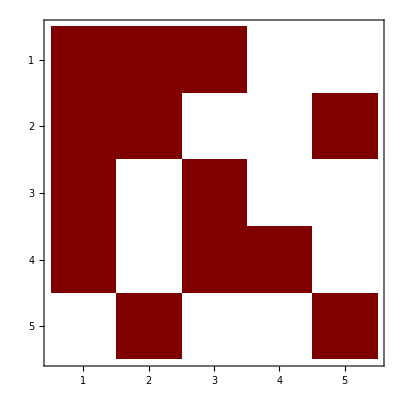

```mathematica
MatrixPlot[ds1[x]]
```

Finally, to get the overall transformation, we use the following command:

```mathematica
t=HistoryConsolidate[ds1];
```

History length for ds1 is 7.

History length for ds1 is 8.

History length for ds1 is 9.

```mathematica
t
```

{{-((3-2 x+3 x^2) ϵ)/(33 (-1+x) (1+x) (-1+2 ϵ)),ϵ/(11 (-1+2 ϵ)),(x ϵ)/((-1+x) (1+x) (-1+2 ϵ)),0,(5 x-35 x ϵ-2 ϵ^2+58 x ϵ^2-2 x^2 ϵ^2)/(22 (-1+x) (1+x) ϵ (-1+2 ϵ))},{-(x (1-7 ϵ+12 ϵ^2))/(33 (-1+x) (1+x) (-1+2 ϵ)),0,(x (1-7 ϵ+12 ϵ^2))/(2 (-1+x) (1+x) (-1+2 ϵ)),-(x (1-7 ϵ+12 ϵ^2))/(6 (-1+x) (1+x) (-1+2 ϵ)),(x (1-7 ϵ+12 ϵ^2))/(22 (-1+x) (1+x) (-1+2 ϵ))},{0,0,0,0,(5 x (1-7 ϵ+12 ϵ^2))/(44 (-1+x) (1+x) ϵ)},{-(x (1-7 ϵ+12 ϵ^2))/(33 (-1+x) (1+x) (-1+2 ϵ)),0,0,(x (1-7 ϵ+12 ϵ^2))/(6 (-1+x) (1+x) (-1+2 ϵ)),(x (1-7 ϵ+12 ϵ^2))/(22 (-1+x) (1+x) (-1+2 ϵ))},{(-3 ϵ+6 x ϵ-3 x^2 ϵ+18 ϵ^2-32 x ϵ^2+18 x^2 ϵ^2-24 ϵ^3+32 x ϵ^3-24 x^2 ϵ^3)/(66 (-1+x) (1+x) (-1+2 ϵ) (1+2 ϵ)),(ϵ+x^2 ϵ-6 ϵ^2-4 x ϵ^2-6 x^2 ϵ^2+8 ϵ^3+16 x ϵ^3+8 x^2 ϵ^3)/(22 (-1+x)^2 (-1+2 ϵ) (1+2 ϵ)),(x ϵ^2-4 x ϵ^3)/((-1+x) (1+x) (-1+2 ϵ) (1+2 ϵ)),0,(-ϵ-8 x ϵ-x^2 ϵ+6 ϵ^2+56 x ϵ^2+6 x^2 ϵ^2-8 ϵ^3-96 x ϵ^3-8 x^2 ϵ^3)/(22 (-1+x) (1+x) (-1+2 ϵ) (1+2 ϵ))}}

Now we can check that the found transformation is correct.

First, we undo all transformations:

```mathematica
Undo[ds1,All]
```

History length for ds1 is 1.

<|x→{{(1-2 x+x^2-6 ϵ+10 x ϵ-6 x^2 ϵ+6 ϵ^2-8 x ϵ^2+6 x^2 ϵ^2)/((-1+x) x (1+x) ϵ),-(2 (-1+x))/(x (1+x)),-(2 (-1+x) (-1+3 ϵ))/(x (1+x) ϵ),-(2 (-1+x))/(x (1+x)),-(2 (-1+x) (1+2 ϵ))/(x (1+x) ϵ)},{-((-1+3 ϵ) (-1+4 ϵ))/((-1+x) (1+x)),-(1+x^2-2 x ϵ)/((-1+x) x (1+x)),(2 (-1+5 ϵ))/((-1+x) (1+x)),(6 ϵ)/((-1+x) (1+x)),0},{((-1+3 ϵ) (-1+4 ϵ) (-1+2 x-x^2+2 ϵ+2 x^2 ϵ))/(2 (-1+x) x (1+x) ϵ),-(-1+2 x-x^2+4 ϵ-4 x ϵ+4 x^2 ϵ)/((-1+x) x (1+x)),-(1-2 x+x^2-6 ϵ+10 x ϵ-6 x^2 ϵ+12 ϵ^2-8 x ϵ^2+12 x^2 ϵ^2)/((-1+x) x (1+x) ϵ),-(-1+2 x-x^2+4 ϵ-4 x ϵ+4 x^2 ϵ)/((-1+x) x (1+x)),-((-1+x) (1+2 ϵ) (-1+3 ϵ))/(x (1+x) ϵ)},{-((-1+3 ϵ) (-1+4 ϵ))/((-1+x) (1+x)),(6 ϵ)/((-1+x) (1+x)),(2 (-1+5 ϵ))/((-1+x) (1+x)),-(1+x^2-2 x ϵ)/((-1+x) x (1+x)),0},{-((-1+4 ϵ) (1+x+x^2-5 ϵ+x ϵ-5 x^2 ϵ+6 ϵ^2-2 x ϵ^2+6 x^2 ϵ^2))/((-1+x) x (1+x) (1+2 ϵ)),(2 ϵ (-1-x-x^2+4 ϵ-6 x ϵ+4 x^2 ϵ))/((-1+x) x (1+x) (1+2 ϵ)),(2 (1+x+x^2-7 ϵ-x ϵ-7 x^2 ϵ+12 ϵ^2-10 x ϵ^2+12 x^2 ϵ^2))/((-1+x) x (1+x) (1+2 ϵ)),(2 ϵ (-1-x-x^2+4 ϵ-6 x ϵ+4 x^2 ϵ))/((-1+x) x (1+x) (1+2 ϵ)),(2 (-1-x^2+2 ϵ-6 x ϵ+2 x^2 ϵ))/((-1+x) x (1+x))}}|>

Now we re-apply the overall tranformation. However, the command below will complain:

```mathematica
Transform[ds1,t]
```

HistoryAppend::chop: Did not change history to avoid overwriting forward entries. Use HistoryChop[ds] first or execute SetOptions[HistoryAppend,HistoryChop→False].

<|x→{{(-9 ϵ-10 x ϵ-9 x^2 ϵ)/(3 (-1+x) x (1+x)),(9 ϵ)/(5 x),-(22 ϵ)/((-1+x) (1+x)),0,0},{-ϵ/x,-((1+x) ϵ)/((-1+x) x),0,0,(4 ϵ)/x},{-(160 ϵ)/(99 (-1+x) (1+x)),0,(4 ϵ)/(3 (-1+x) (1+x)),0,0},{-(80 ϵ)/(33 (-1+x) (1+x)),0,(8 ϵ)/((-1+x) (1+x)),-(4 ϵ)/((-1+x) (1+x)),0},{0,-(4 ϵ)/(5 x),0,0,(2 (1+x^2) ϵ)/((-1+x) x (1+x))}}|>

Athough, the command above returns the transformed matrix, it had no effect on the actual differential system:

```mathematica
ds1[x]===m
```

True

This is made for safety: Undo and Redo simply modifies the pointer to the specific history entry (HistoryIndex[ds1]), while the history list (History[ds1]) remains intact. 
By default, dangerous commands can modify differential system only if HistoryIndex[ds1]===Length[History[ds1]], i.e., when the pointer points to the last entry in history list. Therefore has to explicitly chop off the history list by HistoryChop[ds1] before the transformation is possible.

```mathematica
Length@History[ds1]-HistoryIndex[ds1]
```

8

```mathematica
HistoryChop[ds1];
```

```mathematica
Length@History[ds1]-HistoryIndex[ds1]
```

0

Now we can apply the transformation:

```mathematica
Transform[ds1,t]
```

History length for ds1 is 2.

<|x→{{(-9 ϵ-10 x ϵ-9 x^2 ϵ)/(3 (-1+x) x (1+x)),(9 ϵ)/(5 x),-(22 ϵ)/((-1+x) (1+x)),0,0},{-ϵ/x,-((1+x) ϵ)/((-1+x) x),0,0,(4 ϵ)/x},{-(160 ϵ)/(99 (-1+x) (1+x)),0,(4 ϵ)/(3 (-1+x) (1+x)),0,0},{-(80 ϵ)/(33 (-1+x) (1+x)),0,(8 ϵ)/((-1+x) (1+x)),-(4 ϵ)/((-1+x) (1+x)),0},{0,-(4 ϵ)/(5 x),0,0,(2 (1+x^2) ϵ)/((-1+x) x (1+x))}}|>

```mathematica
Quit
```

## Example #2: many blocks

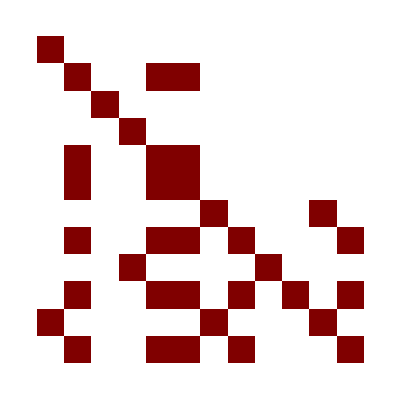
```mathematica
m=-Graphics-;(*m=Get["Data/MatrixY"];*)
```

```mathematica
NewDSystem[ds2,y->m];
```

History length for ds2 is 1.

Successfully created differential system for 12 functions of y.

Diagonal blocks indices are given by

```mathematica
ebi=EntangledBlocksIndices[ds2]
```

Added extra(s) TClosure to current history entry.

{{1},{3},{4},{2,5,6},{9},{7,11},{8,12},{10}}

Now we proceed block-by-block

## Diagonal blocks

#### 1

```mathematica
ii=ebi[[1]]
NewDSystem[b,ds2[[ii,ii]]]
```

{1}

History length for b is 1.

Successfully created differential system for 1 functions of y.

```mathematica
t=VisTransformation[b,y,ϵ,Log->True,Animate->{{1}⟷{2},{3}⟷{4}}];
```

Applied balance {1} ⟷ {2}.
Applied balance {3} ⟷ {4}.

NB: option
	Highlighted→{{1}⟷{2},{3}⟷{4}}
will guide you through the same path,
 while option
	Animate→{{1}⟷{2},{3}⟷{4}}
will press the buttons for you ☺.

```mathematica
Transform[b,t];
```

History length for b is 2.

```mathematica
t=HistoryConsolidate[b]
```

{{y/((-1+y) (1+y))}}

```mathematica
Transform[ds2,t,ii];
```

History length for ds2 is 2.

#### 3

```mathematica
ii=ebi[[2]]
NewDSystem[b,ds2[[ii,ii]]]
```

{3}

History length for b is 1.

Successfully created differential system for 1 functions of y.

```mathematica
t=VisTransformation[b,y,ϵ,Log->True,Animate->{{1}⟷{2},{3}⟷{4}}];
```

Applied balance {1} ⟷ {2}.
Applied balance {3} ⟷ {4}.

NB: option
	Highlighted→{{1}⟷{2},{3}⟷{4}}
will guide you through the same path,
 while option
	Animate→{{1}⟷{2},{3}⟷{4}}
will press the buttons for you ☺.

```mathematica
Transform[b,t];
```

History length for b is 2.

```mathematica
t=HistoryConsolidate[b]
```

{{y/((-1+y) (1+y))}}

```mathematica
Transform[ds2,t,ii];
```

History length for ds2 is 3.

#### 4

```mathematica
ii=ebi[[3]]
NewDSystem[b,ds2[[ii,ii]]]
```

{4}

History length for b is 1.

Successfully created differential system for 1 functions of y.

```mathematica
t=VisTransformation[b,y,ϵ,Animate->{{2}⟷{3},{2}⟷{3},{1}⟷{3},{2}⟷{3},{4}⟷{3},{4}⟷{3},{4}⟷{3}}];
```

```mathematica
Transform[b,t];
```

History length for b is 2.

```mathematica
t=Factor@ExpandNumerator@HistoryConsolidate[b]
```

{{((-1+y)^5 (1+y^2))/(y^3 (1+y))}}

```mathematica
Transform[ds2,t,ii];
```

History length for ds2 is 4.

#### 2,5,6

```mathematica
ii=ebi[[4]]
NewDSystem[b,ds2[[ii,ii]]]
```

{2,5,6}

History length for b is 1.

Successfully created differential system for 3 functions of y.

```mathematica
t=VisTransformation[b,y,ϵ,Animate->{{7}⟷{8},{17}⟷{8},{7}⟷{3},{13}⟷{9},{2}⟷{4},{8}⟷{10},{5}⟷{3},{11}⟷{9},{5}⟷{3},{11}⟷{9}}];
```

```mathematica
Transform[b,t];
```

History length for b is 2.

```mathematica
t=FactorOut[b,y,ϵ,-1]/._C->1;
Transform[b,t];
```

History length for b is 3.

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[b[y]/ϵ,{y,0,1}]]
Transform[b,t];
```

{{1,1,1},{5/2,65/17,-11/7},{47/24,979/408,11/24}}

History length for b is 4.

```mathematica
b[y]
```

{{-(6 (ϵ+y^2 ϵ))/((-1+y) y (1+y)),-(24 ϵ)/(17 y),0},{(17 ϵ)/(2 y),0,(34 ϵ)/(35 y)},{0,-(70 ϵ)/(17 y),(2 (ϵ+y^2 ϵ))/((-1+y) y (1+y))}}

```mathematica
t=Factor@ExpandNumerator@HistoryConsolidate[b]
```

{{-(30 (-1+y) (1+y) ϵ^2)/(y (-27+233 ϵ+230 ϵ^2)),-(30 (1+y^2) ϵ (-1+10 ϵ))/(17 y (-27+233 ϵ+230 ϵ^2)),(6 (-4 y^2-ϵ+26 y^2 ϵ-y^4 ϵ+6 ϵ^2-44 y^2 ϵ^2+6 y^4 ϵ^2))/(7 (-1+y) y (1+y) (-27+233 ϵ+230 ϵ^2))},{(15 (-1+y) (1+y) ϵ^2 (-2+3 ϵ))/(y (-27+233 ϵ+230 ϵ^2)),(30 (1+y^2) ϵ (-2+3 ϵ) (-1+6 ϵ))/(17 y (-27+233 ϵ+230 ϵ^2)),-(6 (-1+y) (1+y) ϵ (-2+3 ϵ) (-1+4 ϵ))/(7 y (-27+233 ϵ+230 ϵ^2))},{-(5 (-1+y) (1+y) ϵ^2 (1+10 y^2+y^4-2 ϵ-25 y^2 ϵ-2 y^4 ϵ+ϵ^2+16 y^2 ϵ^2+y^4 ϵ^2))/(y^3 (-1+ϵ)^2 (-27+233 ϵ+230 ϵ^2)),-(5 (1+y^2) ϵ (-1-16 y^2-y^4+12 ϵ+158 y^2 ϵ+12 y^4 ϵ-21 ϵ^2-326 y^2 ϵ^2-21 y^4 ϵ^2+10 ϵ^3+196 y^2 ϵ^3+10 y^4 ϵ^3))/(17 y^3 (-1+ϵ)^2 (-27+233 ϵ+230 ϵ^2)),(-24 y^4-ϵ-16 y^2 ϵ+210 y^4 ϵ-16 y^6 ϵ-y^8 ϵ+8 ϵ^2+124 y^2 ϵ^2-648 y^4 ϵ^2+124 y^6 ϵ^2+8 y^8 ϵ^2-13 ϵ^3-256 y^2 ϵ^3+794 y^4 ϵ^3-256 y^6 ϵ^3-13 y^8 ϵ^3+6 ϵ^4+160 y^2 ϵ^4-332 y^4 ϵ^4+160 y^6 ϵ^4+6 y^8 ϵ^4)/(7 (-1+y) y^3 (1+y) (-1+ϵ)^2 (-27+233 ϵ+230 ϵ^2))}}

```mathematica
Transform[ds2,t,ii];
```

History length for ds2 is 5.

#### 9

```mathematica
ii=ebi[[5]]
NewDSystem[b,ds2[[ii,ii]]]
```

{9}

History length for b is 1.

Successfully created differential system for 1 functions of y.

```mathematica
t=VisTransformation[b,y,ϵ,Animate->{{1}⟷{2},{4}⟷{3}}];
```

```mathematica
Transform[b,t];
```

History length for b is 2.

```mathematica
t=Factor@ExpandNumerator@HistoryConsolidate[b]
```

{{(1+y^2)/((-1+y) (1+y))}}

```mathematica
Transform[ds2,t,ii];
```

History length for ds2 is 6.

#### 7,11

```mathematica
ii=ebi[[6]]
NewDSystem[b,ds2[[ii,ii]]]
```

{7,11}

History length for b is 1.

Successfully created differential system for 2 functions of y.

```mathematica
t=VisTransformation[b,y,ϵ,Animate->{{2}⟷{3},{6}⟷{7}}];
```

```mathematica
Transform[b,t];
```

History length for b is 2.

```mathematica
t=FactorOut[b,y,ϵ,-1]/._C->1;
Transform[b,t];
```

History length for b is 3.

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[b[y]/ϵ,{y,0,1}]]
Transform[b,t];
```

{{0,1},{1,-2/5}}

History length for b is 4.

```mathematica
t=Factor@ExpandNumerator@HistoryConsolidate[b]
```

{{0,y/((-1+y) (1+y))},{(5 ϵ)/(-2+3 ϵ),-(2 (1+y^2) ϵ)/((-1+y) (1+y) (-2+3 ϵ))}}

```mathematica
Transform[ds2,t,ii];
```

History length for ds2 is 7.

#### 8,12

```mathematica
ii=ebi[[7]]
NewDSystem[b,ds2[[ii,ii]]]
```

{8,12}

History length for b is 1.

Successfully created differential system for 2 functions of y.

```mathematica
t=VisTransformation[b,y,ϵ,Animate->{{4}⟷{6},{12}⟷{8},{2}⟷{3},{10}⟷{11}}];
```

```mathematica
Transform[b,t];
```

History length for b is 2.

```mathematica
t=FactorOut[b,y,ϵ,-1]/._C->1;
Transform[b,t];
```

History length for b is 3.

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[b[y]/ϵ,{y,0,1}]]
Transform[b,t];
```

{{1,0},{0,1}}

History length for b is 4.

```mathematica
t=Factor@ExpandNumerator@HistoryConsolidate[b]
```

{{y/((-1+y) (1+y)),0},{(2 (-1+2 ϵ) (y^2-2 ϵ-y^2 ϵ+y^4 ϵ))/((-1+y) y (1+y) (-1+ϵ) (-2+3 ϵ)),(10 (1+y^2) ϵ (-1+2 ϵ))/(3 y (-1+ϵ) (-2+3 ϵ))}}

```mathematica
Transform[ds2,t,ii];
```

History length for ds2 is 8.

#### 10

```mathematica
ii=ebi[[8]]
NewDSystem[b,ds2[[ii,ii]]]
```

{10}

History length for b is 1.

Successfully created differential system for 1 functions of y.

```mathematica
t=VisTransformation[b,y,ϵ,Animate->{{1}⟷{2},{4}⟷{3}}];
```

```mathematica
Transform[b,t];
```

History length for b is 2.

```mathematica
t=Factor@ExpandNumerator@HistoryConsolidate[b]
```

{{(1+y^2)/((-1+y) (1+y))}}

```mathematica
Transform[ds2,t,ii];
```

History length for ds2 is 9.

### Check

```mathematica
FreeQ[Factor[(ds2[[#,#]][y])/ϵ],ϵ]&/@ebi
```

{True,True,True,True,True,True,True,True}

## Saving intermediate results, quiting, and reloading

```mathematica
DumpSave["ds2",ds2];
```

```mathematica
Quit[]
```

```mathematica
Get["ds2"];
```

## Off-diagonal blocks

```mathematica
t=Fuchsify[ds2,y]
```

{{1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,((1-2 y^2+y^4) (15-38 ϵ+24 ϵ^2))/(y (1+y^2) (-1+2 ϵ)^2),0,0,0,0,1,0,0,0},{0,-(15 (1+y^4) ϵ^2)/(y^2 (-27+233 ϵ+230 ϵ^2)),0,0,-(30 (ϵ-7 y^2 ϵ-y^4 ϵ-y^6 ϵ-6 ϵ^2+10 y^2 ϵ^2+6 y^4 ϵ^2+6 y^6 ϵ^2))/(17 y^2 (1+y^2) (-27+233 ϵ+230 ϵ^2)),(6 (1+y^4) (-ϵ+4 ϵ^2))/(7 y^2 (-27+233 ϵ+230 ϵ^2)),0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0},{0,-(9 (-2 ϵ+14 y^2 ϵ+2 y^4 ϵ+2 y^6 ϵ+5 ϵ^2-35 y^2 ϵ^2-5 y^4 ϵ^2-5 y^6 ϵ^2-3 ϵ^3+21 y^2 ϵ^3+3 y^4 ϵ^3+3 y^6 ϵ^3))/(8 y^2 (1+y^2) (-1+2 ϵ) (-27+233 ϵ+230 ϵ^2)),0,0,-(9 (2 ϵ+2 y^4 ϵ-5 ϵ^2-5 y^4 ϵ^2+3 ϵ^3+3 y^4 ϵ^3))/(17 y^2 (27-287 ϵ+236 ϵ^2+460 ϵ^3)),(9 (-2 ϵ-2 y^2 ϵ+2 y^4 ϵ+2 y^6 ϵ+5 ϵ^2+21 y^2 ϵ^2-5 y^4 ϵ^2-5 y^6 ϵ^2-3 ϵ^3-27 y^2 ϵ^3+3 y^4 ϵ^3+3 y^6 ϵ^3))/(70 y^2 (1+y^2) (-1+2 ϵ) (-27+233 ϵ+230 ϵ^2)),0,0,0,0,0,1}}

```mathematica
Transform[ds2,t];
```

History length for ds2 is 10.

```mathematica
FuchsianQ[ds2[y],y]
```

True

## Total factorization

```mathematica
t=FactorOut[ds2,y,ϵ,-1]/._C->1;
```

```mathematica
t
```

{{1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,(2-7 ϵ+6 ϵ^2)/(3 ϵ (-1+4 ϵ)),0,0,0,0,0},{0,0,0,0,0,0,0,-(2 (-2+11 ϵ-20 ϵ^2+12 ϵ^3))/(3 ϵ (-27+233 ϵ+230 ϵ^2)),0,0,0,0},{0,0,0,0,0,0,0,0,(9 (-15+98 ϵ-176 ϵ^2+96 ϵ^3))/(385 ϵ (-1+2 ϵ)^2),0,0,0},{0,(10 (ϵ+ϵ^2))/(-27+233 ϵ+230 ϵ^2),0,0,0,-(8 (ϵ+ϵ^2))/(7 (-27+233 ϵ+230 ϵ^2)),0,(2 (1-4 ϵ+ϵ^2+6 ϵ^3))/(3 ϵ (-27+233 ϵ+230 ϵ^2)),0,-(10 (-ϵ+2 ϵ^2))/(-27+233 ϵ+230 ϵ^2),0,0},{1,0,0,0,0,0,0,0,0,0,(2-7 ϵ+6 ϵ^2)/(3 ϵ (-1+4 ϵ)),0},{0,(-4+30 ϵ-30 ϵ^2-31 ϵ^3+33 ϵ^4)/(6 ϵ (-1+2 ϵ) (-27+233 ϵ+230 ϵ^2)),0,0,(2 (-4+30 ϵ-30 ϵ^2-31 ϵ^3+33 ϵ^4))/(51 ϵ (-1+2 ϵ) (-27+233 ϵ+230 ϵ^2)),(2 (-2+15 ϵ-42 ϵ^2-2 ϵ^3+57 ϵ^4))/(105 ϵ (-1+2 ϵ) (-27+233 ϵ+230 ϵ^2)),0,0,0,0,0,-(2 (-2+11 ϵ-20 ϵ^2+12 ϵ^3))/(3 ϵ (-27+233 ϵ+230 ϵ^2))}}

```mathematica
Transform[ds2,t];
```

History length for ds2 is 11.

```mathematica
Factor[ds2]
```

History length for ds2 is 12.

```mathematica
FreeQ[ds2[y]/ϵ,ϵ]
```

True

## Example #3: using notations instead of variable change

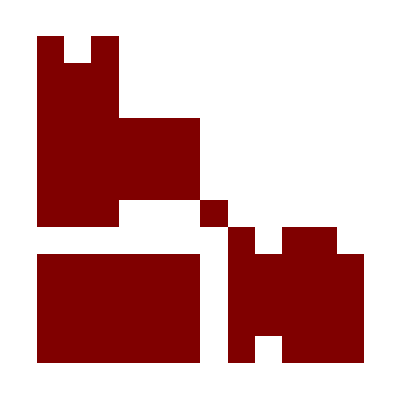
```mathematica
m=-Graphics-;(*m1=Factor[Get["Data/Mi"]/.d->4-2ϵ];*)
```

```mathematica
NewDSystem[ds3,s->m]
```

History length for ds3 is 1.

Successfully created differential system for 12 functions of s.

```mathematica
ebi=EntangledBlocksIndices[m]
```

{{1,2,3},{4,5,6},{7},{8,9,10,11,12}}

## Diagonal blocks

#### 1,2,3

```mathematica
ii=ebi[[1]]
NewDSystem[b,ds3[[ii,ii]]]
```

{1,2,3}

History length for b is 1.

Successfully created differential system for 3 functions of s.

```mathematica
b[]
```

<|s→{{-(-2+3 ϵ)/s,0,2/s},{-(2 (-1+2 ϵ) (-2+3 ϵ) (-3+4 ϵ))/((-4+s) s ϵ),-(2-3 s-8 ϵ+7 s ϵ)/((-4+s) s),(6 (-1+2 ϵ) (-2+3 ϵ))/((-4+s) s ϵ)},{-((-2+3 ϵ) (-3+4 ϵ))/(2 s),-ϵ/2,(-3+4 ϵ)/s}}|>

While using visual tool below, we observe that there are ‘square root’  branching points at s=0 anf s=4. Therefore, we have to make the change of variable. But first we reduce the eigenvalues as much as possible.

```mathematica
t=VisTransformation[b,s,ϵ,Log->True,Animate->{{2}⟷{10},{9}⟷{6},{9}⟷{6},{8}⟷{6}}];
```

Applied balance {2} ⟷ {10}.
Applied balance {9} ⟷ {6}.
Applied balance {9} ⟷ {6}.
Applied balance {8} ⟷ {6}.

NB: option
	Highlighted→{{2}⟷{10},{9}⟷{6},{9}⟷{6},{8}⟷{6}}
will guide you through the same path,
 while option
	Animate→{{2}⟷{10},{9}⟷{6},{9}⟷{6},{8}⟷{6}}
will press the buttons for you ☺.

```mathematica
Transform[b,t];
```

History length for b is 2.

As the number of ‘square root’ points, 2, is less than 4 (cf. arXiv:1707.07856, Section 4), we can use change of variable:

```mathematica
{{stoβ}}=Solve[√((s-4)/s)==β,s];stoβ
```

s→-4/(-1+β^2)

```mathematica
ChangeVar[b,stoβ,β];
```

History length for b is 3.

NB: the second argument of VisTransformation below is the new variable β.

```mathematica
t=VisTransformation[b,β,ϵ,Log->True,Animate->{{6}⟷{12}}];
```

Applied balance {6} ⟷ {12}.

NB: option
	Highlighted→{{6}⟷{12}}
will guide you through the same path,
 while option
	Animate→{{6}⟷{12}}
will press the buttons for you ☺.

```mathematica
Transform[b,t];
```

History length for b is 4.

```mathematica
t=FactorOut[b,β,ϵ,1/2]/._C->1;
```

```mathematica
Transform[b,t];
```

History length for b is 5.

```mathematica
EFormQ[b,ϵ]
```

True

```mathematica
DenominatorsInfo[b,β]
```

{{-1+β,0},{β,0},{1+β,0},{1/β,0}}

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[b[β]/ϵ,{β,0,1}]]
```

{{1,1,1},{-127/1149,-5/47,-7/61},{-431/1149,-193/517,-23/61}}

```mathematica
Transform[b,t];b[β]
```

History length for b is 6.

{{-(2 β ϵ)/((-1+β) (1+β)),0,-(4596 ϵ)/(61 (-1+β) (1+β))},{0,0,(2068 ϵ)/(61 (-1+β) (1+β))},{(488 ϵ)/(383 (-1+β) (1+β)),(366 ϵ)/(517 (-1+β) (1+β)),(2 (5 ϵ+2 β^2 ϵ))/((-1+β) β (1+β))}}

The overall transformation depends now on β rather than s:

```mathematica
t=HistoryConsolidate[b]
```

{{(4 (12-24 β^2+12 β^4-151 ϵ+251 β^2 ϵ-97 β^4 ϵ-3 β^6 ϵ+682 ϵ^2-826 β^2 ϵ^2+174 β^4 ϵ^2+18 β^6 ϵ^2))/(1149 (-1+β)^2 (1+β)^2 (-30-1103 ϵ+2330 ϵ^2)),(16 (3-6 β^2+3 β^4-31 ϵ+56 β^2 ϵ-25 β^4 ϵ+103 ϵ^2-154 β^2 ϵ^2+55 β^4 ϵ^2))/(517 (-1+β)^2 (1+β)^2 (-30-1103 ϵ+2330 ϵ^2)),(16 (27 β ϵ^2-26 β^3 ϵ^2+3 β^5 ϵ^2))/(61 (-1+β)^2 (1+β)^2 (-30-1103 ϵ+2330 ϵ^2))},{-(2 (42-36 β^2-6 β^4-467 ϵ+270 β^2 ϵ+53 β^4 ϵ+1070 ϵ^2-548 β^2 ϵ^2-114 β^4 ϵ^2-696 ϵ^3+336 β^2 ϵ^3+72 β^4 ϵ^3))/(1149 (-1+β) (1+β) (-30-1103 ϵ+2330 ϵ^2)),-(8 (6-6 β^2-59 ϵ+47 β^2 ϵ+131 ϵ^2-97 β^2 ϵ^2-84 ϵ^3+60 β^2 ϵ^3))/(517 (-1+β) (1+β) (-30-1103 ϵ+2330 ϵ^2)),-(8 (-18 β ϵ+6 β^3 ϵ+51 β ϵ^2-17 β^3 ϵ^2-36 β ϵ^3+12 β^3 ϵ^3))/(61 (-1+β) (1+β) (-30-1103 ϵ+2330 ϵ^2))},{(2 (24-24 β^2-299 ϵ+242 β^2 ϵ+9 β^4 ϵ+1430 ϵ^2-748 β^2 ϵ^2-66 β^4 ϵ^2-1432 ϵ^3+624 β^2 ϵ^3+72 β^4 ϵ^3))/(1149 (-1+β) (1+β) (-30-1103 ϵ+2330 ϵ^2)),(8 (6-6 β^2-65 ϵ+59 β^2 ϵ+247 ϵ^2-185 β^2 ϵ^2-228 ϵ^3+156 β^2 ϵ^3))/(517 (-1+β) (1+β) (-30-1103 ϵ+2330 ϵ^2)),(8 (39 β ϵ^2-9 β^3 ϵ^2-52 β ϵ^3+12 β^3 ϵ^3))/(61 (-1+β) (1+β) (-30-1103 ϵ+2330 ϵ^2))}}

We can reduce the β appearance using QuolyMod and RuleToNotation functions:

```mathematica
βnotation=RuleToNotation[stoβ,β]
```

β→-4+s-s β^2

The above line should be undestood as “β is defined by the polynomial equation -4+s-s,β^2=0”. 
Now we  can ‘mod out’ any expression wrt the constraint -4+s-s,β^2=0.

```mathematica
t=QuolyMod[t,βnotation]
```

{{(4 (12 s+12 ϵ-106 s ϵ-12 s^2 ϵ-72 ϵ^2+228 s ϵ^2+106 s^2 ϵ^2+3 s^3 ϵ^2))/(1149 s (-30-1103 ϵ+2330 ϵ^2)),(4 (12-100 ϵ-6 s ϵ+220 ϵ^2+44 s ϵ^2+s^2 ϵ^2))/(517 (-30-1103 ϵ+2330 ϵ^2)),(4 β (12 ϵ^2+20 s ϵ^2+s^2 ϵ^2))/(61 (-30-1103 ϵ+2330 ϵ^2))},{-(4 (12-24 s-106 ϵ+188 s ϵ+18 s^2 ϵ+228 ϵ^2-388 s ϵ^2-51 s^2 ϵ^2-144 ϵ^3+240 s ϵ^3+36 s^2 ϵ^3))/(1149 s (-30-1103 ϵ+2330 ϵ^2)),-(4 (-12+94 ϵ+6 s ϵ-194 ϵ^2-17 s ϵ^2+120 ϵ^3+12 s ϵ^3))/(517 (-30-1103 ϵ+2330 ϵ^2)),-(4 β (12 ϵ+6 s ϵ-34 ϵ^2-17 s ϵ^2+24 ϵ^3+12 s ϵ^3))/(61 (-30-1103 ϵ+2330 ϵ^2))},{(4 (-12 s-18 ϵ+130 s ϵ+6 s^2 ϵ+132 ϵ^2-440 s ϵ^2-77 s^2 ϵ^2-144 ϵ^3+384 s ϵ^3+92 s^2 ϵ^3))/(1149 s (-30-1103 ϵ+2330 ϵ^2)),(4 (-12+118 ϵ+3 s ϵ-370 ϵ^2-31 s ϵ^2+312 ϵ^3+36 s ϵ^3))/(517 (-30-1103 ϵ+2330 ϵ^2)),(4 β (-18 ϵ^2-15 s ϵ^2+24 ϵ^3+20 s ϵ^3))/(61 (-30-1103 ϵ+2330 ϵ^2))}}

The result is necessarily the polynomial of β with degree one less that that of the constraint (i.e., deg=1 in our case).

Now, instead of changing variable in the whole matrix ds3, we introduce the corresponding notation:

```mathematica
AddNotation[ds3,βnotation];
```

History length for ds3 is 2.

```mathematica
Variables[ds3]
```

{s}

```mathematica
Notations[ds3]
```

{β→-4+s-s β^2}

NB: it is crucial to introduce notation before making transformation depending on it! Otherwise, Libra would assume β is some parameter independent of s and will calculate wrongly D[t,s] and, therefore, the whole transformation!

```mathematica
Transform[ds3,t,ii];
```

History length for ds3 is 3.

History length for ds3 is 3.

History length for ds3 is 3.

```mathematica
EFormQ[ds3[[ii,ii]][s],ϵ]
```

True

Note that the corresponding block now depends both on s and β. The dependence on the latter parameter is confined to be first-order polynomial:

```mathematica
ds3[[ii,ii]][s]
```

{{ϵ/s,0,(2298 β ϵ)/(61 (-4+s))},{0,0,-(1034 β ϵ)/(61 (-4+s))},{-(244 β ϵ)/(383 (-4+s)),-(183 β ϵ)/(517 (-4+s)),(8 ϵ-7 s ϵ)/((-4+s) s)}}

#### 4,5,6

```mathematica
ii=ebi[[2]]
NewDSystem[b,ds3[[ii,ii]]];
```

{4,5,6}

History length for b is 1.

Successfully created differential system for 3 functions of s.

```mathematica
Denominators[b]
```

Added extra(s) Denominators to current history entry.

{s,1+s,1-5 ϵ-s ϵ+4 ϵ^2+2 s ϵ^2}

Note that there are apparent (fake) singularities at zeros of 1-5 ϵ-s ϵ+4 ϵ^2+2 s ϵ^2. Since this denominator is linear in s, we can treat it on general ground, even with the visual tool below.

```mathematica
t=VisTransformation[b,s,ϵ,Log->True,Animate->{{6}⟷{7},{4}⟷{7},{3}⟷{5}}];
```

Applied balance {6} ⟷ {7}.
Applied balance {4} ⟷ {7}.
Applied balance {3} ⟷ {5}.

NB: option
	Highlighted→{{6}⟷{7},{4}⟷{7},{3}⟷{5}}
will guide you through the same path,
 while option
	Animate→{{6}⟷{7},{4}⟷{7},{3}⟷{5}}
will press the buttons for you ☺.

```mathematica
Transform[b,t];
```

History length for b is 2.

```mathematica
Denominators[b]
```

Added extra(s) Denominators to current history entry.

{s,1+s}

```mathematica
t=FactorOut[b,s,ϵ,-2]/._C->1;
```

```mathematica
Transform[b,t];
```

History length for b is 3.

```mathematica
EFormQ[b,ϵ]
```

True

```mathematica
DenominatorsInfo[b,s]
```

{{s,0},{1+s,0},{1/s,0}}

```mathematica
b[s]
```

{{(361 ϵ+100 s ϵ)/(125 s (1+s)),(3316 ϵ-425 s ϵ)/(3125 s (1+s)),-(3 (-1164 ϵ+25 s ϵ))/(1250 s (1+s))},{(2 (43 ϵ+25 s ϵ))/(5 s (1+s)),-(3 (-97 ϵ+75 s ϵ))/(125 s (1+s)),(221 ϵ-25 s ϵ)/(25 s (1+s))},{-(6 (47 ϵ+25 s ϵ))/(25 s (1+s)),(11 (-147 ϵ+25 s ϵ))/(625 s (1+s)),(-1027 ϵ-125 s ϵ)/(125 s (1+s))}}

In order to simplify the numerical coefficients a bit, we will ‘shake’ the system by diagonalizing residues:

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[b[s]/ϵ,{s,-1,-1}]];
Transform[b,t]
```

History length for b is 4.

<|s→{{(-4 ϵ-3 s ϵ)/(s (1+s)),(87 ϵ)/(205 s),-(5829 ϵ)/(10250 s)},{(101 ϵ)/(29 s),(86 ϵ)/(205 s),(4693 ϵ)/(10250 s)},{(50 ϵ)/(3 s),(380 ϵ)/(41 s),(119 ϵ)/(205 s)}}|>

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[b[s]/ϵ,{s,0,-1}]];
Transform[b,t]
```

History length for b is 5.

<|s→{{(9 ϵ+5 s ϵ)/(9 s (1+s)),-(29 ϵ)/(3 (1+s)),0},{(52 ϵ)/(783 (1+s)),(-18 ϵ-5 s ϵ)/(9 s (1+s)),ϵ/s},{-(8 ϵ)/(261 (1+s)),-(2 ϵ)/(3 (1+s)),-(2 ϵ)/s}}|>

```mathematica
t=HistoryConsolidate[b]
```

{{-(125 (9-54 ϵ-5 s ϵ+81 ϵ^2+12 s ϵ^2))/(348 s (3-15 ϵ+23 ϵ^2)),(125 (-ϵ+3 ϵ^2))/(4 (3-15 ϵ+23 ϵ^2)),(125 ϵ^2)/(4 (3-15 ϵ+23 ϵ^2))},{-(125 (3-18 ϵ-2 s ϵ+27 ϵ^2+10 s ϵ^2+12 ϵ^3-16 s ϵ^3-36 ϵ^4+8 s ϵ^4))/(348 s (1+ϵ) (3-15 ϵ+23 ϵ^2)),(125 (-ϵ+5 ϵ^2-8 ϵ^3+4 ϵ^4))/(4 (1+ϵ) (3-15 ϵ+23 ϵ^2)),(125 (-1+2 ϵ)^2 (-1+2 ϵ-s ϵ+s ϵ^2))/(4 s (1+ϵ) (3-15 ϵ+23 ϵ^2))},{-(125 (-1+2 ϵ) (-18 ϵ-15 s ϵ-s^2 ϵ+54 ϵ^2+52 s ϵ^2+6 s^2 ϵ^2))/(348 s (1+s) (3-15 ϵ+23 ϵ^2)),(125 (-1+2 ϵ) (s ϵ+2 ϵ^2))/(4 (1+s) (3-15 ϵ+23 ϵ^2)),-(125 (-1+2 ϵ) (-ϵ+ϵ^2))/(2 (3-15 ϵ+23 ϵ^2))}}

```mathematica
Transform[ds3,t,ii];
```

History length for ds3 is 4.

History length for ds3 is 4.

History length for ds3 is 4.

```mathematica
EFormQ[ds3[[ii,ii]][s],ϵ]
```

True

```mathematica
ds3[[ii,ii]][s]
```

{{(9 ϵ+5 s ϵ)/(9 s (1+s)),-(29 ϵ)/(3 (1+s)),0},{(52 ϵ)/(783 (1+s)),(-18 ϵ-5 s ϵ)/(9 s (1+s)),ϵ/s},{-(8 ϵ)/(261 (1+s)),-(2 ϵ)/(3 (1+s)),-(2 ϵ)/s}}

#### 7

```mathematica
ii=ebi[[3]]
NewDSystem[b,ds3[[ii,ii]]];
```

{7}

History length for b is 1.

Successfully created differential system for 1 functions of s.

```mathematica
Denominators[b]
```

Added extra(s) Denominators to current history entry.

{s}

```mathematica
t=VisTransformation[b,s,ϵ,Animate->{{1}⟷{2}}];
```

```mathematica
Transform[b,t];
```

History length for b is 2.

```mathematica
Denominators[b]
```

Added extra(s) Denominators to current history entry.

{}

```mathematica
b[]
```

<|s→{{0}}|>

```mathematica
t=HistoryConsolidate[b]
```

{{1/s}}

```mathematica
Transform[ds3,t,ii];
```

History length for ds3 is 5.

History length for ds3 is 5.

History length for ds3 is 5.

«2 more identical outputs»

```mathematica
EFormQ[ds3[[ii,ii]][s],ϵ]
```

True

```mathematica
ds3[[ii,ii]][s]
```

{{0}}

#### 8,9,10,11,12

```mathematica
ii=ebi[[4]]
NewDSystem[b,ds3[[ii,ii]]];
```

{8,9,10,11,12}

History length for b is 1.

Successfully created differential system for 5 functions of s.

```mathematica
Denominators[b]
```

Added extra(s) Denominators to current history entry.

{s,4+s^2}

Using visual tool, we see the ‘square root’ branching points at s=±2i. Again we first reduce to some extent other singular points.

```mathematica
t=VisTransformation[b,s,ϵ,Log->True,Animate->{{21}⟷{6},{3,4,5}⟷{16,17,18}}];
```

Applied balance {21} ⟷ {6}.
Applied balance {3, 4, 5} ⟷ {16, 17, 18}.

NB: option
	Highlighted→{{21}⟷{6},{3,4,5}⟷{16,17,18}}
will guide you through the same path,
 while option
	Animate→{{21}⟷{6},{3,4,5}⟷{16,17,18}}
will press the buttons for you ☺.

```mathematica
Transform[b,t];
```

History length for b is 2.

```mathematica
Denominators[b]
```

Added extra(s) Denominators to current history entry.

{s,4+s^2}

We could have used the variable change √((s+2i)/(s-2i)), similar to what we have had previously. But that would potentially introduce imaginary unit in the matrix.
Here we choose another variable change, which also has square root branching points at s=±2i.

```mathematica
{{stoξ}}=Solve[√(4+s^2)-s==2ξ,s]
```

{{s→(1-ξ^2)/ξ}}

```mathematica
ChangeVar[b,stoξ,ξ];Factor[b]
```

History length for b is 3.

History length for b is 4.

A special care is needed when the singular points belong to algebraic extension of ℚ. The reason is that those algebraic extensions may unnecessarily appear in the final matrix. In praticular, in our present example we have 2i, the root of s^2+4=0, and we would prefer that it does not appear in the transformation and in the final matrix.
Libra has special tools for treating irreducible denominators, but here we will apply a poor man approach by chosing the balances in a ‘symmetric way’ and hoping the the overall transformation will not depend on i.

```mathematica
t=VisTransformation[b,ξ,ϵ,Log->True,Animate->{{5}⟷{15},{25}⟷{20},{1}⟷{15},{21}⟷{20},{1}⟷{15},{21}⟷{20}}];
```

Applied balance {5} ⟷ {15}.
Applied balance {25} ⟷ {20}.
Applied balance {1} ⟷ {15}.
Applied balance {21} ⟷ {20}.
Applied balance {1} ⟷ {15}.
Applied balance {21} ⟷ {20}.

NB: option
	Highlighted→{{5}⟷{15},{25}⟷{20},{1}⟷{15},{21}⟷{20},{1}⟷{15},{21}⟷{20}}
will guide you through the same path,
 while option
	Animate→{{5}⟷{15},{25}⟷{20},{1}⟷{15},{21}⟷{20},{1}⟷{15},{21}⟷{20}}
will press the buttons for you ☺.

Let us check if we a lucky and t is real:

```mathematica
t=ExpandNumerator@ExpandDenominator@Factor[t];
FreeQ[t,_Complex]
```

True

Yes, we are. So we apply the transformation:

```mathematica
Transform[b,t];
```

History length for b is 5.

```mathematica
t=FactorOut[b,ξ,ϵ,-2]/._C->1;
```

```mathematica
Transform[b,t];
```

History length for b is 6.

```mathematica
EFormQ[b,ϵ]
```

True

```mathematica
DenominatorsInfo[b,ξ]
```

{{-1+ξ,0},{ξ,0},{1+ξ,0},{1+ξ^2,0},{1/ξ,0}}

```mathematica
t=Transpose@JDSpace[SeriesCoefficient[b[ξ]/ϵ,{ξ,0,1}]];
Transform[b,t]
```

History length for b is 7.

<|ξ→{{-(3 (ϵ+ϵ ξ^2))/((-1+ξ) ξ (1+ξ)),0,0,0,-ϵ/(11 (-1+ξ) (1+ξ))},{0,0,0,0,(3 ϵ)/(4 (-1+ξ) (1+ξ))},{0,0,(ϵ+ϵ ξ^2)/((-1+ξ) ξ (1+ξ)),0,-(9 ϵ)/(22 ξ)},{0,0,0,(2 (ϵ+ϵ ξ^2))/((-1+ξ) ξ (1+ξ)),(9 ϵ)/(22 ξ)},{(176 ϵ)/(3 (-1+ξ) (1+ξ)),(64 ϵ)/(9 (-1+ξ) (1+ξ)),-(88 ϵ)/(9 ξ),-(440 ϵ)/(9 ξ),-(6 ϵ (-1+ξ) (1+ξ))/(ξ (1+ξ^2))}}|>

```mathematica
ξnotation=RuleToNotation[stoξ,ξ]
```

ξ→1-s ξ-ξ^2

```mathematica
t=QuolyMod[HistoryConsolidate[b],ξnotation]
```

{{1,0,(2 (-1+5 ϵ))/(9 s ϵ),(2 (-1+4 ϵ))/(9 s ϵ),0},{(8 (ϵ-9 ϵ^2+20 ϵ^3))/(3 s^2 (-1-ϵ+2 ϵ^2)),-(16 (ϵ-9 ϵ^2+20 ϵ^3))/(99 s^2 (-1-ϵ+2 ϵ^2)),(1-11 ϵ+38 ϵ^2-40 ϵ^3)/(9 s (-1-ϵ+2 ϵ^2)),-(2 (-1+12 ϵ-47 ϵ^2+60 ϵ^3))/(9 s (-1-ϵ+2 ϵ^2)),((ϵ-9 ϵ^2+20 ϵ^3) (s+2 ξ))/(22 s^2 (-1-ϵ+2 ϵ^2))},{(-1+9 ϵ-20 ϵ^2)/(6 s ϵ),-(2 (1-9 ϵ+20 ϵ^2))/(99 s ϵ),(1-9 ϵ+20 ϵ^2)/(18 s ϵ),(1-9 ϵ+20 ϵ^2)/(18 s ϵ),0},{(1-9 ϵ+20 ϵ^2)/(6 s ϵ),(2 (1-9 ϵ+20 ϵ^2))/(99 s ϵ),(1-9 ϵ+20 ϵ^2)/(18 s ϵ),(1-9 ϵ+20 ϵ^2)/(18 s ϵ),0},{(2 (6 ϵ-31 ϵ^2+41 ϵ^3))/(3 (-2+11 ϵ-19 ϵ^2+10 ϵ^3)),-(16 (-ϵ^2+5 ϵ^3))/(99 (-2+11 ϵ-19 ϵ^2+10 ϵ^3)),(-8+92 ϵ-364 ϵ^2-s^2 ϵ^2+580 ϵ^3+8 s^2 ϵ^3-300 ϵ^4-15 s^2 ϵ^4)/(18 s ϵ (-2+11 ϵ-19 ϵ^2+10 ϵ^3)),-(2 (2-22 ϵ+84 ϵ^2+s^2 ϵ^2-128 ϵ^3-8 s^2 ϵ^3+64 ϵ^4+15 s^2 ϵ^4))/(9 s ϵ (-2+11 ϵ-19 ϵ^2+10 ϵ^3)),(s ϵ-8 s ϵ^2+15 s ϵ^3+2 ϵ ξ-16 ϵ^2 ξ+30 ϵ^3 ξ)/(44 (-2+11 ϵ-19 ϵ^2+10 ϵ^3))}}

```mathematica
AddNotation[ds3,ξnotation];
Variables[ds3]
Notations[ds3]
```

History length for ds3 is 6.

{s}

{β→-4+s-s β^2,ξ→1-s ξ-ξ^2}

```mathematica
Transform[ds3,t,ii];
```

History length for ds3 is 7.

```mathematica
t
```

{{1,0,(2 (-1+5 ϵ))/(9 s ϵ),(2 (-1+4 ϵ))/(9 s ϵ),0},{(8 (ϵ-9 ϵ^2+20 ϵ^3))/(3 s^2 (-1-ϵ+2 ϵ^2)),-(16 (ϵ-9 ϵ^2+20 ϵ^3))/(99 s^2 (-1-ϵ+2 ϵ^2)),(1-11 ϵ+38 ϵ^2-40 ϵ^3)/(9 s (-1-ϵ+2 ϵ^2)),-(2 (-1+12 ϵ-47 ϵ^2+60 ϵ^3))/(9 s (-1-ϵ+2 ϵ^2)),((ϵ-9 ϵ^2+20 ϵ^3) (s+2 ξ))/(22 s^2 (-1-ϵ+2 ϵ^2))},{(-1+9 ϵ-20 ϵ^2)/(6 s ϵ),-(2 (1-9 ϵ+20 ϵ^2))/(99 s ϵ),(1-9 ϵ+20 ϵ^2)/(18 s ϵ),(1-9 ϵ+20 ϵ^2)/(18 s ϵ),0},{(1-9 ϵ+20 ϵ^2)/(6 s ϵ),(2 (1-9 ϵ+20 ϵ^2))/(99 s ϵ),(1-9 ϵ+20 ϵ^2)/(18 s ϵ),(1-9 ϵ+20 ϵ^2)/(18 s ϵ),0},{(2 (6 ϵ-31 ϵ^2+41 ϵ^3))/(3 (-2+11 ϵ-19 ϵ^2+10 ϵ^3)),-(16 (-ϵ^2+5 ϵ^3))/(99 (-2+11 ϵ-19 ϵ^2+10 ϵ^3)),(-8+92 ϵ-364 ϵ^2-s^2 ϵ^2+580 ϵ^3+8 s^2 ϵ^3-300 ϵ^4-15 s^2 ϵ^4)/(18 s ϵ (-2+11 ϵ-19 ϵ^2+10 ϵ^3)),-(2 (2-22 ϵ+84 ϵ^2+s^2 ϵ^2-128 ϵ^3-8 s^2 ϵ^3+64 ϵ^4+15 s^2 ϵ^4))/(9 s ϵ (-2+11 ϵ-19 ϵ^2+10 ϵ^3)),(s ϵ-8 s ϵ^2+15 s ϵ^3+2 ϵ ξ-16 ϵ^2 ξ+30 ϵ^3 ξ)/(44 (-2+11 ϵ-19 ϵ^2+10 ϵ^3))}}

```mathematica
ds3
```

ds3

```mathematica
EFormQ[ds3[[ii,ii]][s],ϵ]
```

True

```mathematica
ds3[[ii,ii]][s]
```

{{-(3 ϵ)/s,0,0,0,(-s ϵ-2 ϵ ξ)/(11 s (4+s^2))},{0,0,0,0,(3 ϵ (s+2 ξ))/(4 s (4+s^2))},{0,0,ϵ/s,0,(9 ϵ (s+2 ξ))/(22 (4+s^2))},{0,0,0,(2 ϵ)/s,-(9 ϵ (s+2 ξ))/(22 (4+s^2))},{(176 ϵ (s+2 ξ))/(3 s (4+s^2)),(64 ϵ (s+2 ξ))/(9 s (4+s^2)),(88 (s ϵ+2 ϵ ξ))/(9 (4+s^2)),(440 (s ϵ+2 ϵ ξ))/(9 (4+s^2)),-(6 s ϵ)/(4+s^2)}}

### Check&Save

```mathematica
EFormQ[ds3[[#,#]][s],ϵ]&/@ebi
```

{True,True,True,True}

```mathematica
DumpSave["Data/ds3.tmp",ds3];
```

## Off-diagonal blocks

```mathematica
Get["Data/ds3.tmp"]
```

```mathematica
obi=OffDiagonalBlocksIndices[ds3]
```

Added extra(s) TClosure to current history entry.

{{{4,5,6},{1,2,3}},{{7},{1,2,3}},{{8,9,10,11,12},{4,5,6}},{{8,9,10,11,12},{1,2,3}}}

Note that it is essential that off-diagonal blocks are reduced in a special order, e.g., as they appear in OffDiagonalBlocksIndices[ds3]

### {4,5,6},{1,2,3}

```mathematica
block=obi[[1]]
```

{{4,5,6},{1,2,3}}

```mathematica
t=FuchsifyBlock[ds3,s,block];
```

History length for b$10661 is 2.

```mathematica
Transform[ds3,t,Flatten[block]];
```

History length for ds3 is 8.

```mathematica
FuchsianQ[ds3[[Flatten[block],Flatten[block]]],s]
```

True

### {7},{1,2,3}

```mathematica
block=obi[[2]]
```

{{7},{1,2,3}}

```mathematica
t=FuchsifyBlock[ds3,s,block];
```

History length for b$11609 is 2.

```mathematica
Transform[ds3,t,Flatten[block]];
```

History length for ds3 is 9.

```mathematica
FuchsianQ[ds3[[Flatten[block],Flatten[block]]],s]
```

True

### {8,9,10,11,12},{4,5,6}

```mathematica
block=obi[[3]]
```

{{8,9,10,11,12},{4,5,6}}

```mathematica
t=FuchsifyBlock[ds3,s,block];
```

History length for b$12015 is 2.

```mathematica
Transform[ds3,t,Flatten[block]];
```

History length for ds3 is 10.

```mathematica
FuchsianQ[ds3[[Flatten[block],Flatten[block]]],s]
```

True

### {8,9,10,11,12},{1,2,3}: two notations, manual

NB: Don’t rely on FuchsianQ when there are notations!

```mathematica
block=obi[[4]]
```

{{8,9,10,11,12},{1,2,3}}

As of the time this tutorial is written, FuchsifyBlock may treat at most one notation. Since block {1,2,3}×{1,2,3} uses β and {8,9,10,11,12}×{8,9,10,11,12} uses ξ, in the off-diagonalblock both of them appear. Therefore, FuchsifyBlock fails:

```mathematica
t=FuchsifyBlock[ds3,s,block]
```

FuchsifyBlock::notas: More that one notation involved. Not implemented yet. Aborting...

$Aborted

Therefore, we have to do it in a semi-manual way. We start by copying the corresponding submatrix. 
Do not foget to copy notations!

```mathematica
NewDSystem[b,ds3[[Flatten@Reverse@block,Flatten@Reverse@block]]];
AddNotation[b,#]&/@(Notations[ds3]/.Association->List);
```

History length for b is 1.

Successfully created differential system for 8 functions of s.

History length for b is 2.

History length for b is 3.

Both β and ξ enter the matrix at most to the first power since the corresponding polynomials are quadratic:

```mathematica
Values@Notations[b]
```

{-4+s-s β^2,1-s ξ-ξ^2}

We first examine denominators:

```mathematica
DenominatorsInfo[b,s]
```

{{-4+s,0},{s,1},{1+s,0},{4+s^2,2},{1/s,0}}

#### Denominator s

It is temptful to start with s=0. However, there is a problem here. Note that β→∞ when s→0. Therefore, when we fuchsify other points (which requires β in the numerator), we can spoil the behaviour at s=0. The same thing relates to s=∞ and ξ (se below).

#### Denominator 4+s^2

Nothing especially bad happens with β and ξ:

```mathematica
Solve[#==0]&/@(Values@Notations[b]/.s->-2I)
```

{{{β→-√(1-2 ⅈ)},{β→√(1-2 ⅈ)}},{{ξ→ⅈ},{ξ→ⅈ}}}

```mathematica
den=4+s^2;(*denominator*)
```

```mathematica
r=2;(*Poincare rank*)
```

Since den is quadratic in s, we allow for the first power of s also:

```mathematica
t=IdentityMatrix@Length@b;
cs=Array[Subscript[c, ##]&,{5,3,2,2,2}];
t[[{4,5,6,7,8},{1,2,3}]]=(((cs.{1,β}).{1,ξ}).{1,s})/den^r
```

{{(c_(1,1,1,1,1)+β c_(1,1,1,1,2)+ξ (c_(1,1,1,2,1)+β c_(1,1,1,2,2))+s (c_(1,1,2,1,1)+β c_(1,1,2,1,2)+ξ (c_(1,1,2,2,1)+β c_(1,1,2,2,2))))/((4+s^2)^2),(c_(1,2,1,1,1)+β c_(1,2,1,1,2)+ξ (c_(1,2,1,2,1)+β c_(1,2,1,2,2))+s (c_(1,2,2,1,1)+β c_(1,2,2,1,2)+ξ (c_(1,2,2,2,1)+β c_(1,2,2,2,2))))/((4+s^2)^2),(c_(1,3,1,1,1)+β c_(1,3,1,1,2)+ξ (c_(1,3,1,2,1)+β c_(1,3,1,2,2))+s (c_(1,3,2,1,1)+β c_(1,3,2,1,2)+ξ (c_(1,3,2,2,1)+β c_(1,3,2,2,2))))/((4+s^2)^2)},{(c_(2,1,1,1,1)+β c_(2,1,1,1,2)+ξ (c_(2,1,1,2,1)+β c_(2,1,1,2,2))+s (c_(2,1,2,1,1)+β c_(2,1,2,1,2)+ξ (c_(2,1,2,2,1)+β c_(2,1,2,2,2))))/((4+s^2)^2),(c_(2,2,1,1,1)+β c_(2,2,1,1,2)+ξ (c_(2,2,1,2,1)+β c_(2,2,1,2,2))+s (c_(2,2,2,1,1)+β c_(2,2,2,1,2)+ξ (c_(2,2,2,2,1)+β c_(2,2,2,2,2))))/((4+s^2)^2),(c_(2,3,1,1,1)+β c_(2,3,1,1,2)+ξ (c_(2,3,1,2,1)+β c_(2,3,1,2,2))+s (c_(2,3,2,1,1)+β c_(2,3,2,1,2)+ξ (c_(2,3,2,2,1)+β c_(2,3,2,2,2))))/((4+s^2)^2)},{(c_(3,1,1,1,1)+β c_(3,1,1,1,2)+ξ (c_(3,1,1,2,1)+β c_(3,1,1,2,2))+s (c_(3,1,2,1,1)+β c_(3,1,2,1,2)+ξ (c_(3,1,2,2,1)+β c_(3,1,2,2,2))))/((4+s^2)^2),(c_(3,2,1,1,1)+β c_(3,2,1,1,2)+ξ (c_(3,2,1,2,1)+β c_(3,2,1,2,2))+s (c_(3,2,2,1,1)+β c_(3,2,2,1,2)+ξ (c_(3,2,2,2,1)+β c_(3,2,2,2,2))))/((4+s^2)^2),(c_(3,3,1,1,1)+β c_(3,3,1,1,2)+ξ (c_(3,3,1,2,1)+β c_(3,3,1,2,2))+s (c_(3,3,2,1,1)+β c_(3,3,2,1,2)+ξ (c_(3,3,2,2,1)+β c_(3,3,2,2,2))))/((4+s^2)^2)},{(c_(4,1,1,1,1)+β c_(4,1,1,1,2)+ξ (c_(4,1,1,2,1)+β c_(4,1,1,2,2))+s (c_(4,1,2,1,1)+β c_(4,1,2,1,2)+ξ (c_(4,1,2,2,1)+β c_(4,1,2,2,2))))/((4+s^2)^2),(c_(4,2,1,1,1)+β c_(4,2,1,1,2)+ξ (c_(4,2,1,2,1)+β c_(4,2,1,2,2))+s (c_(4,2,2,1,1)+β c_(4,2,2,1,2)+ξ (c_(4,2,2,2,1)+β c_(4,2,2,2,2))))/((4+s^2)^2),(c_(4,3,1,1,1)+β c_(4,3,1,1,2)+ξ (c_(4,3,1,2,1)+β c_(4,3,1,2,2))+s (c_(4,3,2,1,1)+β c_(4,3,2,1,2)+ξ (c_(4,3,2,2,1)+β c_(4,3,2,2,2))))/((4+s^2)^2)},{(c_(5,1,1,1,1)+β c_(5,1,1,1,2)+ξ (c_(5,1,1,2,1)+β c_(5,1,1,2,2))+s (c_(5,1,2,1,1)+β c_(5,1,2,1,2)+ξ (c_(5,1,2,2,1)+β c_(5,1,2,2,2))))/((4+s^2)^2),(c_(5,2,1,1,1)+β c_(5,2,1,1,2)+ξ (c_(5,2,1,2,1)+β c_(5,2,1,2,2))+s (c_(5,2,2,1,1)+β c_(5,2,2,1,2)+ξ (c_(5,2,2,2,1)+β c_(5,2,2,2,2))))/((4+s^2)^2),(c_(5,3,1,1,1)+β c_(5,3,1,1,2)+ξ (c_(5,3,1,2,1)+β c_(5,3,1,2,2))+s (c_(5,3,2,1,1)+β c_(5,3,2,1,2)+ξ (c_(5,3,2,2,1)+β c_(5,3,2,2,2))))/((4+s^2)^2)}}

We could have applied the transformation to the whole matrix, but it would take a lot of time. In this case even the principal part is too complicated for transformation, so we pick out only those terms which enter the equations:
Diagonal blocks  ∝(4+s^2)^-1
Off-diagonal block  ∝(4+s^2)^(-1-r)

```mathematica
Pp=SeriesCoefficientMod[b[s],{s->den,-r-1}]/den^(r+1);
(Pp[[#,#] ]=SeriesCoefficientMod[b[[#,#]][s],{s->den,-1}]/den;)&/@EntangledBlocksIndices[b];
```

Added extra(s) TClosure to current history entry.

```mathematica
Ppnew=Transform[Pp,t,{s,Notations[b]/.Association->List}];
```

```mathematica
eqs=Flatten[CoefficientList[SeriesCoefficientMod[Ppnew,{s->den,-r-1}],{β,ξ,s}]];
```

```mathematica
csrules=GaussSolve[eqs,Flatten[cs]];
```

```mathematica
t=t/.csrules;
```

```mathematica
FreeQ[t,Alternatives@@Flatten[cs]]
```

True

```mathematica
Transform[b,t];
```

History length for b is 4.

```mathematica
DenominatorsInfo[b,s]
```

{{-4+s,0},{s,1},{1+s,0},{4+s^2,1},{1/s,0}}

Now we repeat with r=1

```mathematica
r=1;(*Poincare rank*)
```

```mathematica
t=IdentityMatrix@Length@b;
cs=Array[Subscript[c, ##]&,{5,3,2,2,2}];
t[[{4,5,6,7,8},{1,2,3}]]=(((cs.{1,β}).{1,ξ}).{1,s})/den^r;
```

```mathematica
Pp=SeriesCoefficientMod[b[s],{s->den,-r-1}]/den^(r+1);
(Pp[[#,#] ]=SeriesCoefficientMod[b[[#,#]][s],{s->den,-1}]/den;)&/@EntangledBlocksIndices[b];
```

Added extra(s) TClosure to current history entry.

```mathematica
Ppnew=Transform[Pp,t,{s,Notations[b]/.Association->List}];
```

```mathematica
eqs=Flatten[CoefficientList[SeriesCoefficientMod[Ppnew,{s->den,-r-1}],{β,ξ,s}]];
```

```mathematica
csrules=GaussSolve[eqs,Flatten[cs]];
```

```mathematica
t=t/.csrules;
```

```mathematica
FreeQ[t,Alternatives@@Flatten[cs]]
```

True

```mathematica
Transform[b,t];
```

History length for b is 5.

```mathematica
DenominatorsInfo[b,s]
```

{{-4+s,0},{s,1},{1+s,0},{4+s^2,0},{1/s,0}}

So, we have obtained the Fuchsian form at s=±2i. Good time to save

```mathematica
DumpSave["Data/b.tmp",b];
```

#### s→∞

The limit s→∞ should be analyzed with care. Notation β goes to 1, but ξ migh go to ∞ too. Threfore, we shoud better eliminate terms of the form ξ/s.

However, there are no such terms:

```mathematica
Factor@Coefficient[SeriesCoefficient[b[s],{s,∞,1}],ξ,1]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

#### Denominator s

We start from s=0. The idea is the following: we make a template matrix, apply the transformation and solve for the coefficients to reduce the pole order.

```mathematica
EntangledBlocksIndices[b]
```

Added extra(s) TClosure to current history entry.

{{1,2,3},{4,5,6,7,8}}

```mathematica
den=s;(*denominator*)
```

```mathematica
r=1;(*Poincare rank*)
```

```mathematica
t=IdentityMatrix@Length@b;
cs=Array[Subscript[c, ##]&,{5,3,2,2}];
t[[{4,5,6,7,8},{1,2,3}]]=((cs.{1,β}).{1,ξ})/den^r
```

{{(c_(1,1,1,1)+β c_(1,1,1,2)+ξ (c_(1,1,2,1)+β c_(1,1,2,2)))/s,(c_(1,2,1,1)+β c_(1,2,1,2)+ξ (c_(1,2,2,1)+β c_(1,2,2,2)))/s,(c_(1,3,1,1)+β c_(1,3,1,2)+ξ (c_(1,3,2,1)+β c_(1,3,2,2)))/s},{(c_(2,1,1,1)+β c_(2,1,1,2)+ξ (c_(2,1,2,1)+β c_(2,1,2,2)))/s,(c_(2,2,1,1)+β c_(2,2,1,2)+ξ (c_(2,2,2,1)+β c_(2,2,2,2)))/s,(c_(2,3,1,1)+β c_(2,3,1,2)+ξ (c_(2,3,2,1)+β c_(2,3,2,2)))/s},{(c_(3,1,1,1)+β c_(3,1,1,2)+ξ (c_(3,1,2,1)+β c_(3,1,2,2)))/s,(c_(3,2,1,1)+β c_(3,2,1,2)+ξ (c_(3,2,2,1)+β c_(3,2,2,2)))/s,(c_(3,3,1,1)+β c_(3,3,1,2)+ξ (c_(3,3,2,1)+β c_(3,3,2,2)))/s},{(c_(4,1,1,1)+β c_(4,1,1,2)+ξ (c_(4,1,2,1)+β c_(4,1,2,2)))/s,(c_(4,2,1,1)+β c_(4,2,1,2)+ξ (c_(4,2,2,1)+β c_(4,2,2,2)))/s,(c_(4,3,1,1)+β c_(4,3,1,2)+ξ (c_(4,3,2,1)+β c_(4,3,2,2)))/s},{(c_(5,1,1,1)+β c_(5,1,1,2)+ξ (c_(5,1,2,1)+β c_(5,1,2,2)))/s,(c_(5,2,1,1)+β c_(5,2,1,2)+ξ (c_(5,2,2,1)+β c_(5,2,2,2)))/s,(c_(5,3,1,1)+β c_(5,3,1,2)+ξ (c_(5,3,2,1)+β c_(5,3,2,2)))/s}}

We could have applied the transformation to the whole matrix, but it would take a lot of time. So we apply it to the principal part of expansion:

```mathematica
Pp=Sum[SeriesCoefficientMod[b[s],{s->den,k}] den^k,{k,-r-1,-1}];
```

Normal[Series[b[s],{s,0,-1}]] would have the same effect:

```mathematica
Factor[Pp-Normal[Series[b[s],{s,0,-1}]]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
eqs=Flatten[CoefficientList[SeriesCoefficientMod[Transform[Pp,t,{s,Notations[b]/.Association->List}],{s->den,-r-1}],{β,ξ}]];
```

```mathematica
csrules=GaussSolve[eqs,Flatten[cs]];
```

```mathematica
t=t/.csrules;
```

```mathematica
FreeQ[t,Alternatives@@Flatten[cs]]
```

True

```mathematica
Transform[b,t];
```

History length for b is 6.

```mathematica
DenominatorsInfo[b,s]
```

{{-4+s,0},{s,0},{1+s,0},{4+s^2,0},{1/s,0}}

We might have thought that the system b is Fuchsian at s=0 now, but there is a subtle point here: when s goes to zero  β goes to infinity. Therefore, terms of the form β/s are not Fuchsian.  Thus, we eliminate them. Basically, this kind of complications resist the fully automated approach.

One way to see this is to examine our notations at s=0:

```mathematica
Simplify[Values@Notations[b]/.s->0]
```

{-4,1-ξ^2}

We see that the first notation corresponds to the equation -4==0, which has no solutions.

```mathematica
r=0;(*Formal Poincare rank*)
```

```mathematica
Factor@Coefficient[SeriesCoefficient[b[s],{s,∞,1}],ξ,1]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

Note that ξ might go to -s or to 0 when s goes to ∞. Therefore, not to spoil infinity, we can not use ξ upstairs

```mathematica
Notations[ds3][ξ]
```

{β→-4+s-s β^2,ξ→1-s ξ-ξ^2}[ξ]

```mathematica
t=IdentityMatrix@Length@b;
cs=Array[Subscript[c, ##]&,{5,3,1}];
t[[{4,5,6,7,8},{1,2,3}]]=(cs*β).{1(*,ξ (*not allowed*)*)}
```

{{β c_(1,1,1),β c_(1,2,1),β c_(1,3,1)},{β c_(2,1,1),β c_(2,2,1),β c_(2,3,1)},{β c_(3,1,1),β c_(3,2,1),β c_(3,3,1)},{β c_(4,1,1),β c_(4,2,1),β c_(4,3,1)},{β c_(5,1,1),β c_(5,2,1),β c_(5,3,1)}}

We could have applied the transformation to the whole matrix, but it would take a lot of time. So we apply it to the principal part of expansion.
NB: When s→0, β grows as s^(-1/2), so the terms β s^0∝s^(-1/2) are irrelevant (smaller than s^-1).

```mathematica
Pp=Sum[SeriesCoefficientMod[b[s],{s->den,k}] den^k,{k,-r-1,-1}];
```

Normal[Series[b[s],{s,0,-1}]] would have the same effect:

```mathematica
Factor[Pp-Normal[Series[b[s],{s,0,-1}]]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

Indeed, there are dangerous terms:

```mathematica
Factor[Coefficient[Pp,β]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,(32 ϵ^2 (-2+3 ϵ) (-3+4 ϵ) (-2+7 ϵ) ξ)/(61 s (1+ϵ) (-1+5 ϵ) (-30-1103 ϵ+2330 ϵ^2)),0,0,0,0,0},{0,0,-(264 ϵ^2 (-2+3 ϵ) (-3+4 ϵ) (-2+7 ϵ) ξ)/(61 s (1+ϵ) (-1+5 ϵ) (-30-1103 ϵ+2330 ϵ^2)),0,0,0,0,0},{0,0,(72 ϵ (-2+3 ϵ) (-3+4 ϵ) (1+6 ϵ))/(61 s (1+ϵ) (-30-1103 ϵ+2330 ϵ^2)),0,0,0,0,0},{0,0,-(72 ϵ (-2+3 ϵ) (-3+4 ϵ) (1+8 ϵ))/(61 s (1+ϵ) (-30-1103 ϵ+2330 ϵ^2)),0,0,0,0,0},{0,0,-(352 ϵ (-2+3 ϵ) (-3+4 ϵ) (1+4 ϵ) (-2+7 ϵ))/(61 s (1+ϵ) (-1+5 ϵ) (-30-1103 ϵ+2330 ϵ^2)),0,0,0,0,0}}

```mathematica
eqs=Flatten[CoefficientList[Coefficient[SeriesCoefficientMod[Transform[Pp,t,{s,Notations[b]/.Association->List}],{s->den,-r-1}],β],ξ]];
```

The fact that the equations are compatible comes out as a surprise:

```mathematica
Length[eqs]
Length[Flatten@cs]
```

24

15

```mathematica
csrules=GaussSolve[eqs,Flatten[cs]]
```

{c_(1,1,1)→0,c_(5,1,1)→0,c_(1,2,1)→0,c_(5,2,1)→0,c_(1,3,1)→0,c_(5,3,1)→(704 ϵ (-12+76 ϵ-143 ϵ^2+84 ϵ^3))/(61 (30+983 ϵ-6892 ϵ^2+3805 ϵ^3+11650 ϵ^4)),c_(2,1,1)→0,c_(2,2,1)→0,c_(2,3,1)→0,c_(3,1,1)→0,c_(3,2,1)→0,c_(3,3,1)→-(144 (6 ϵ-17 ϵ^2+12 ϵ^3))/(61 (-30-1133 ϵ+1227 ϵ^2+2330 ϵ^3)),c_(4,1,1)→0,c_(4,2,1)→0,c_(4,3,1)→(144 (6 ϵ-17 ϵ^2+12 ϵ^3))/(61 (-30-1133 ϵ+1227 ϵ^2+2330 ϵ^3))}

```mathematica
t=Factor[t/.csrules];
```

```mathematica
FreeQ[t,Alternatives@@Flatten[cs]]
```

True

Application will take some time:

```mathematica
Transform[b,t];
```

History length for b is 7.

```mathematica
DenominatorsInfo[b,s]
```

{{-4+s,0},{s,0},{1+s,0},{4+s^2,0},{1/s,0}}

Let us check if β is absent in s^-1 terms:

```mathematica
Coefficient[SeriesCoefficientMod[b[s],{s->den,-1}],β]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

Let us check that we have not spoiled behaviour at ∞

```mathematica
Coefficient[SeriesCoefficient[b[s],{s,∞,1}],ξ,1]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

So, we have obtained the Fuchsian form at s=1. Good time to save

```mathematica
DumpSave["Data/b.tmp",b];
```

#### β→∞,ξ→∞

```mathematica
Get["Data/b.tmp"];
```

One might get an impression that we are done, but we should also consider the points where ξ and/or β go to ∞. Since ξ→∞ implies s→∞, and β→∞ implies s→0, we seem to be done.

```mathematica
Coefficient[Normal[SeriesCoefficient[ds3[s],{s,0,-1}]],β]
```

{{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-(2 (36 ϵ^2-672 ϵ^3+5203 ϵ^4-21500 ϵ^5+49885 ϵ^6-59004 ϵ^7+13420 ϵ^8+47136 ϵ^9-49984 ϵ^10+15360 ϵ^11))/(61 (-1+ϵ)^2 (-1+2 ϵ)^2 (-1+4 ϵ)^2 (-30-863 ϵ+10704 ϵ^2-35185 ϵ^3+34950 ϵ^4)),0,0,0,0,0,0,0,0,0},{0,0,-(33 (-36 ϵ^2+816 ϵ^3-7699 ϵ^4+39656 ϵ^5-122269 ϵ^6+232200 ϵ^7-268564 ϵ^8+179328 ϵ^9-60992 ϵ^10+7680 ϵ^11))/(122 (-1+ϵ)^2 (-1+2 ϵ)^2 (-1+4 ϵ)^2 (-30-863 ϵ+10704 ϵ^2-35185 ϵ^3+34950 ϵ^4)),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(88 (36 ϵ^2 ξ-720 ϵ^3 ξ+6035 ϵ^4 ξ-27552 ϵ^5 ξ+74013 ϵ^6 ξ-116736 ϵ^7 ξ+98468 ϵ^8 ξ-28352 ϵ^9 ξ-12992 ϵ^10 ξ+7680 ϵ^11 ξ))/(61 (-1+ϵ)^2 (-1+2 ϵ)^2 (-1+4 ϵ)^2 (-30-863 ϵ+10704 ϵ^2-35185 ϵ^3+34950 ϵ^4)),0,0,0,0,0,0,0,0,0}}

```mathematica
EntangledBlocksIndices
```

EntangledBlocksIndices

#### Consolidating and applying

```mathematica
DenominatorsInfo[b,s]
```

{{-4+s,0},{s,0},{1+s,0},{4+s^2,0},{1/s,0}}

```mathematica
t=HistoryConsolidate[b];
```

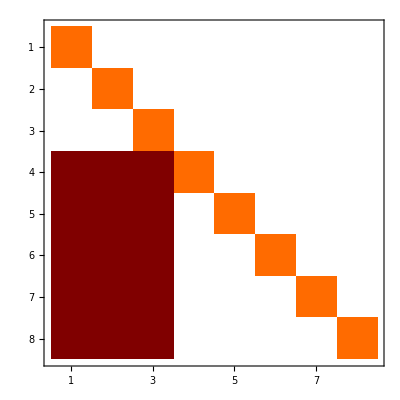

```mathematica
MatrixPlot[t]
```

Now we apply the transformation to ds3

NB: when creating the matrix b, we used Flatten@Reverse@block to have a familiar lower-triangular form (pay attention to Reverse). Therefore, we use the same when applying the overall transformation:

```mathematica
Transform[ds3,t,Flatten@Reverse@block];
```

History length for ds3 is 11.

```mathematica
DenominatorsInfo[ds3[[Flatten[block],Flatten[block]]],s]
```

{{-4+s,0},{s,0},{1+s,0},{4+s^2,0},{1/s,0}}

```mathematica
Coefficient[SeriesCoefficient[ds3[[Flatten[block],Flatten[block]]][s],{s,0,-1}],β]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

Let us check that we have not spoiled behaviour at ∞

```mathematica
Coefficient[SeriesCoefficient[b[s],{s,∞,1}],ξ,1]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

### Saving

```mathematica
DumpSave["Data/ds3.tmp1",ds3]
```

{ds3}

## Overall factorization

Since we have notations, it is not safe to use FactorOut. It is better to rely on the approach which also works for multivariate setup: sampling and factoring out dependence.

Ok, so we get samples in a few points . But we have to substitute notations

```mathematica
Get["Data/ds3.tmp1"]
```

```mathematica
βξcoefs=Coefficient[Coefficient[ds3[s],β,#1],ξ,#2]&@@@{{0,0},{0,1},{1,0},{1,1}};
```

```mathematica
samples=Flatten[βξcoefs/.({s->#}&/@RandomInteger[{5,30},3]),1];
```

There should be a transformation which eliminates ϵ from samples/ϵ, and we can search for it useing FactorDependence:

```mathematica
Variables[samples]
```

{ϵ}

```mathematica
t=FactorDependence[samples/ϵ,ϵ,-2]/._C->1;
```

```mathematica
Transform[ds3,t];
```

History length for ds3 is 12.

```mathematica
EFormQ[ds3,ϵ]
```

True

```mathematica
Unprotect[ds3];Save["Data/ds3.res",ds3];
```

```mathematica
Quit[]
```

## Check

```mathematica
Get["Data/ds3.res"];
ds3[s]
```

{{ϵ/s,0,(2298 β ϵ)/(61 (-4+s)),0,0,0,0,0,0,0,0,0},{0,0,-(1034 β ϵ)/(61 (-4+s)),0,0,0,0,0,0,0,0,0},{-(244 β ϵ)/(383 (-4+s)),-(183 β ϵ)/(517 (-4+s)),(8 ϵ-7 s ϵ)/((-4+s) s),0,0,0,0,0,0,0,0,0},{-(3659787472 ϵ)/(12187071442125 (1+s)),-(116 (131112+213673 s) ϵ)/(92317370625 s (1+s)),-(149220544 β ϵ)/(119816161875 (-4+s)),((9+5 s) ϵ)/(9 s (1+s)),-(29 ϵ)/(3 (1+s)),0,0,0,0,0,0,0},{-(176 (68903001+59581442 s) ϵ)/(36561214326375 s (1+s)),-(4 (20441988+19368695 s) ϵ)/(276952111875 s (1+s)),-(1004084312 β ϵ)/(1078345456875 (-4+s)),(52 ϵ)/(783 (1+s)),-((18+5 s) ϵ)/(9 s (1+s)),ϵ/s,0,0,0,0,0,0},{(176 (7445115+6011029 s) ϵ)/(12187071442125 s (1+s)),(8 (1835568+1753007 s) ϵ)/(92317370625 s (1+s)),-(80591104 β ϵ)/(119816161875 (-4+s)),-(8 ϵ)/(261 (1+s)),-(2 ϵ)/(3 (1+s)),-(2 ϵ)/s,0,0,0,0,0,0},{-(1540 ϵ)/(1651113 s),-(30 ϵ)/(22513 s),(2200 β ϵ)/(613599 (-4+s)),0,0,0,0,0,0,0,0,0},{(8 (-14340860 ϵ+134496871 s ϵ+130911656 s^2 ϵ+268993742 ϵ ξ+268993742 s ϵ ξ))/(292489714611 s (4+4 s+s^2+s^3)),(2 (-330244 ϵ+9691322 s ϵ+9608761 s^2 ϵ+19382644 ϵ ξ+19382644 s ϵ ξ))/(4874357169 s (4+4 s+s^2+s^3)),0,-(625 (8 ϵ+7 s ϵ+9 s^2 ϵ+14 ϵ ξ+14 s ϵ ξ))/(8613 s (4+4 s+s^2+s^3)),(625 (-4 ϵ+10 s ϵ+9 s^2 ϵ+20 ϵ ξ+20 s ϵ ξ))/(198 s (4+4 s+s^2+s^3)),(3125 ϵ (s+2 ξ))/(66 s (4+s^2)),0,-(3 ϵ)/s,0,0,0,(-s ϵ-2 ϵ ξ)/(11 s (4+s^2))},{(22 (97456820 ϵ-51380911 s ϵ-110132666 s^2 ϵ+20778990 s^3 ϵ-268993742 ϵ ξ-268993742 s ϵ ξ))/(97496571537 s (4+4 s+s^2+s^3)),(2116720 ϵ-7904846 s ϵ-9162142 s^2 ϵ+446619 s^3 ϵ-19382644 ϵ ξ-19382644 s ϵ ξ)/(295415586 s (4+4 s+s^2+s^3)),0,-(625 (-20 ϵ-16 s ϵ-33 s^2 ϵ+3 s^3 ϵ-56 ϵ ξ-56 s ϵ ξ))/(4176 s (1+s) (4+s^2)),(625 (16 ϵ+2 s ϵ-6 s^2 ϵ+3 s^3 ϵ-20 ϵ ξ-20 s ϵ ξ))/(24 s (1+s) (4+s^2)),(625 (12 ϵ-10 s ϵ+3 s^2 ϵ-20 ϵ ξ))/(16 s (4+s^2)),0,0,0,0,0,(3 ϵ (s+2 ξ))/(4 s (4+s^2))},{-(8 (182150310 ϵ+153468590 s ϵ+112786013 s^2 ϵ+105615583 s^3 ϵ+134496871 s ϵ ξ+134496871 s^2 ϵ ξ))/(32498857179 s (4+4 s+s^2+s^3)),-(2 (-3144 ϵ-663632 s ϵ+4844875 s^2 ϵ+4679753 s^3 ϵ+9691322 s ϵ ξ+9691322 s^2 ϵ ξ))/(541595241 s (4+4 s+s^2+s^3)),-(5904 β ϵ)/(29219 (-4+s)),(625 (32 ϵ+7 s ϵ+15 s^2 ϵ+14 ϵ ξ+14 s ϵ ξ))/(1914 (4+4 s+s^2+s^3)),-(625 (24 ϵ+16 s ϵ+11 s^2 ϵ+9 s^3 ϵ+10 s ϵ ξ+10 s^2 ϵ ξ))/(22 s (4+4 s+s^2+s^3)),-(625 (22 ϵ+13 s^2 ϵ+15 s ϵ ξ))/(22 s (4+s^2)),0,0,0,ϵ/s,0,(9 ϵ (s+2 ξ))/(22 (4+s^2))},{(8 (98891974 ϵ+70210254 s ϵ+91971429 s^2 ϵ+84800999 s^3 ϵ+134496871 s ϵ ξ+134496871 s^2 ϵ ξ))/(32498857179 s (4+4 s+s^2+s^3)),(2 (-5794144 ϵ-6454632 s ϵ+3397125 s^2 ϵ+3232003 s^3 ϵ+9691322 s ϵ ξ+9691322 s^2 ϵ ξ))/(541595241 s (4+4 s+s^2+s^3)),(5904 β ϵ)/(29219 (-4+s)),-(625 (20 ϵ+84 s ϵ+19 s^2 ϵ+35 s^3 ϵ+28 s ϵ ξ+28 s^2 ϵ ξ))/(3828 s (4+4 s+s^2+s^3)),(625 (32 ϵ+24 s ϵ+13 s^2 ϵ+11 s^3 ϵ+10 s ϵ ξ+10 s^2 ϵ ξ))/(22 s (4+4 s+s^2+s^3)),(625 ϵ (64+31 s^2+30 s ξ))/(44 s (4+s^2)),0,0,0,0,(2 ϵ)/s,-(9 ϵ (s+2 ξ))/(22 (4+s^2))},{(176 (-124339408 ϵ-13489428 s ϵ+107001827 s^2 ϵ+49930072 s^3 ϵ+135654800 ϵ ξ-530807868 s ϵ ξ-666462668 s^2 ϵ ξ))/(292489714611 s (4+4 s+s^2+s^3)),(4 (-8307376 ϵ-4291604 s ϵ+7052366 s^2 ϵ+4275009 s^3 ϵ+6050080 ϵ ξ-39889512 s ϵ ξ-45939592 s^2 ϵ ξ))/(443123379 s (4+4 s+s^2+s^3)),(1805893936 β ϵ)/(15528174579 (-4+s)),-(625 (28 ϵ-16 s ϵ+103 s^2 ϵ+87 s^3 ϵ+8 ϵ ξ+108 s ϵ ξ+100 s^2 ϵ ξ))/(783 s (4+4 s+s^2+s^3)),(625 (-40 ϵ-20 s ϵ+56 s^2 ϵ+51 s^3 ϵ+16 ϵ ξ+72 s ϵ ξ+56 s^2 ϵ ξ))/(9 s (4+4 s+s^2+s^3)),(1250 (-20 ϵ+3 s ϵ+37 s^2 ϵ+6 ϵ ξ+39 s ϵ ξ))/(9 s (4+s^2)),0,(176 (s ϵ+2 ϵ ξ))/(3 s (4+s^2)),(64 (s ϵ+2 ϵ ξ))/(9 s (4+s^2)),(88 (s ϵ+2 ϵ ξ))/(9 (4+s^2)),(440 (s ϵ+2 ϵ ξ))/(9 (4+s^2)),-(6 s ϵ)/(4+s^2)}}

```mathematica
Notations[ds3]
```

{β→-4+s-s β^2,ξ→1-s ξ-ξ^2}

```mathematica
T=HistoryConsolidate[ds3];
```

```mathematica
Put[{T,Notations[ds3]},"Data/ds3Transformation&Notations"]
```